```mathematica
<<MASSToolbox`
<<MASSToolbox`Style`
```

## Build a RBC model from scratch ...

### Compound information

```mathematica
bigg2inchi=Import["/Users/niko/work/Code/Mixed/Chemoinformatics199/Mappings/bigg2inchi/bigg2inchi.m.gz"];
```

### Map

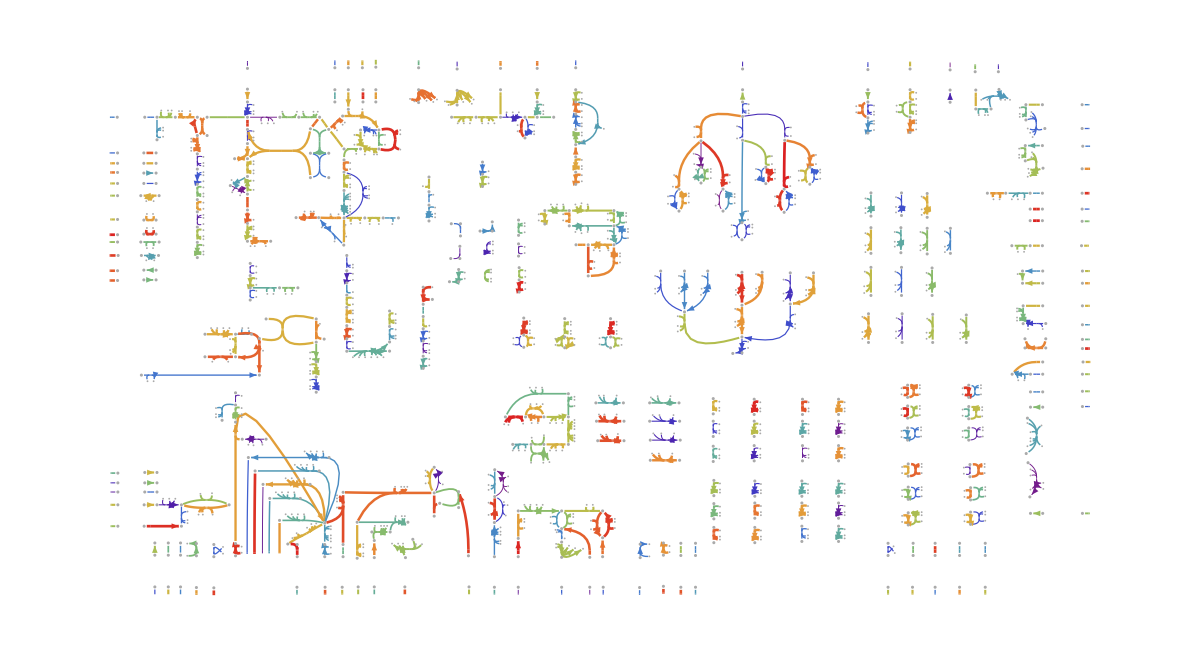

```mathematica
SetDirectory[NotebookDirectory[]];
{cmpdPos,rxnPos,textPos}=importBIGGmap["../data/iAB-RBC-238/iAB-RBC-283-Map.svg"];
fakeData=#->RandomReal[{-1,1}]&/@rxnPos[[All,1]];
drawPathway[cmpdPos,rxnPos,{},ImageSize->1200,Boundary->False,ReactionData->fakeData,ReactionStyle->{Arrowheads->0.005}]
```

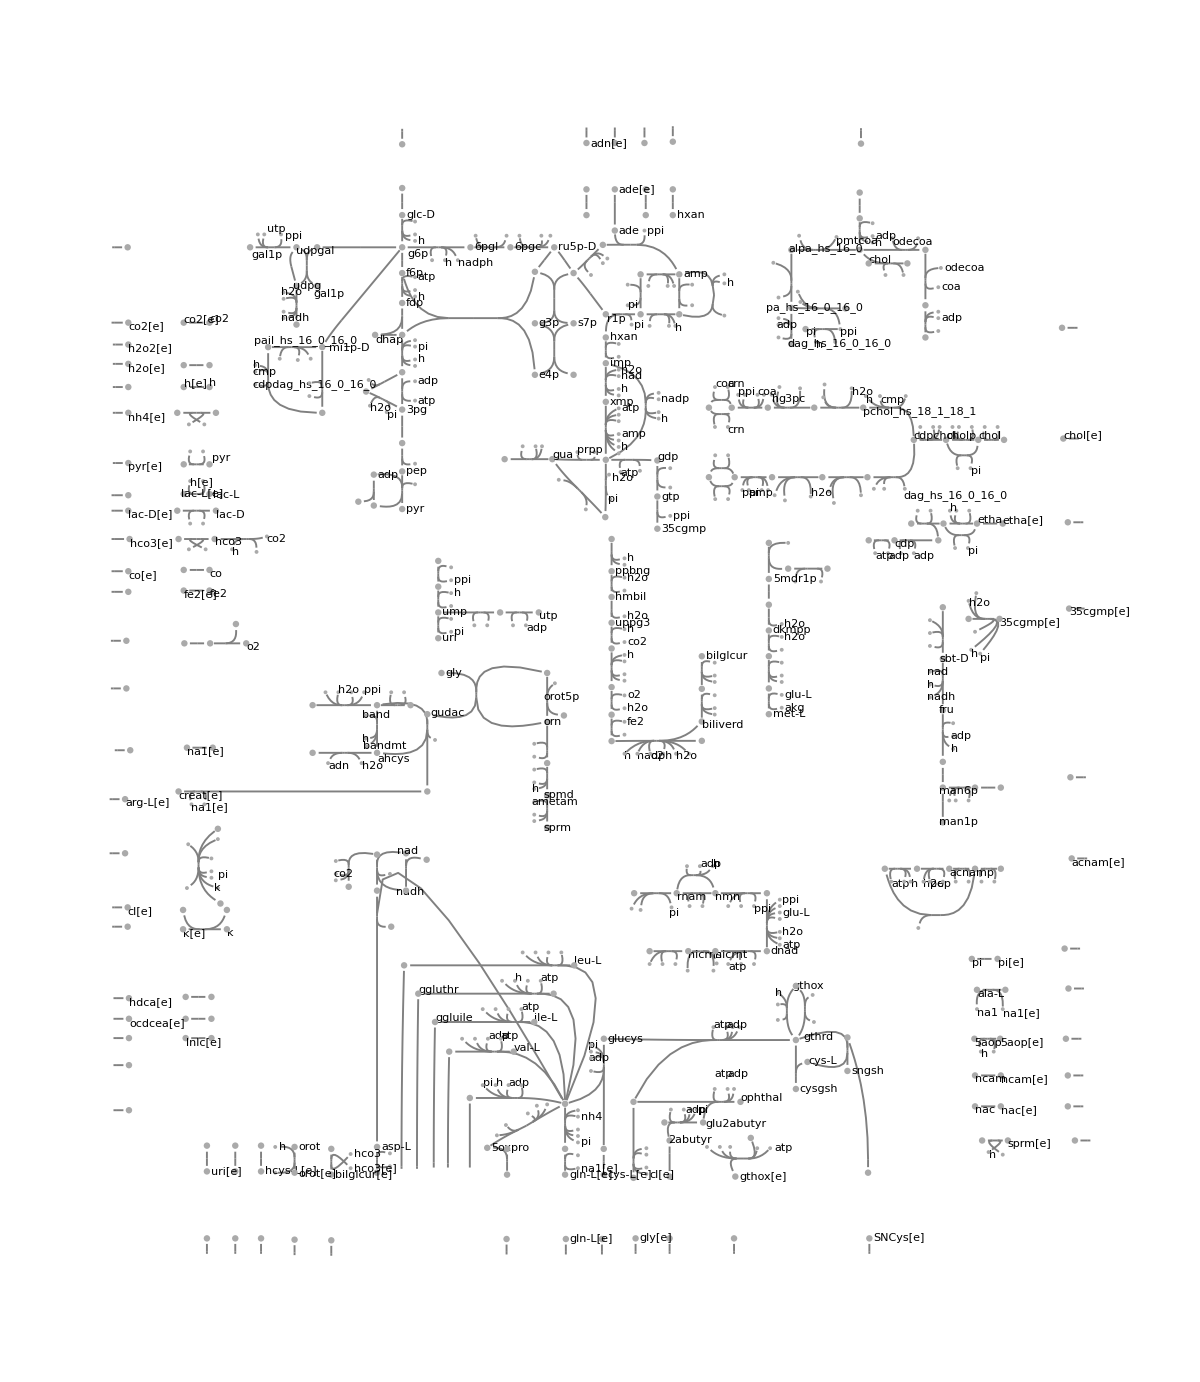

```mathematica
SetDirectory[NotebookDirectory[]];
{cmpdPos,rxnPos,textPos}=importBIGGmap["../data/iAB-RBC-238/iAB-RBC-283-ReducedMap.svg"];
drawPathway[cmpdPos,rxnPos,Flatten@textPos,ImageSize->1200,"TextStyle"->{FontFamily->"Arial",FontSize->Scaled[0.004]},ReactionStyle->{"DefaultStyle"->{Thickness[0.001],GrayLevel[0.5]}},Boundary->False]
```

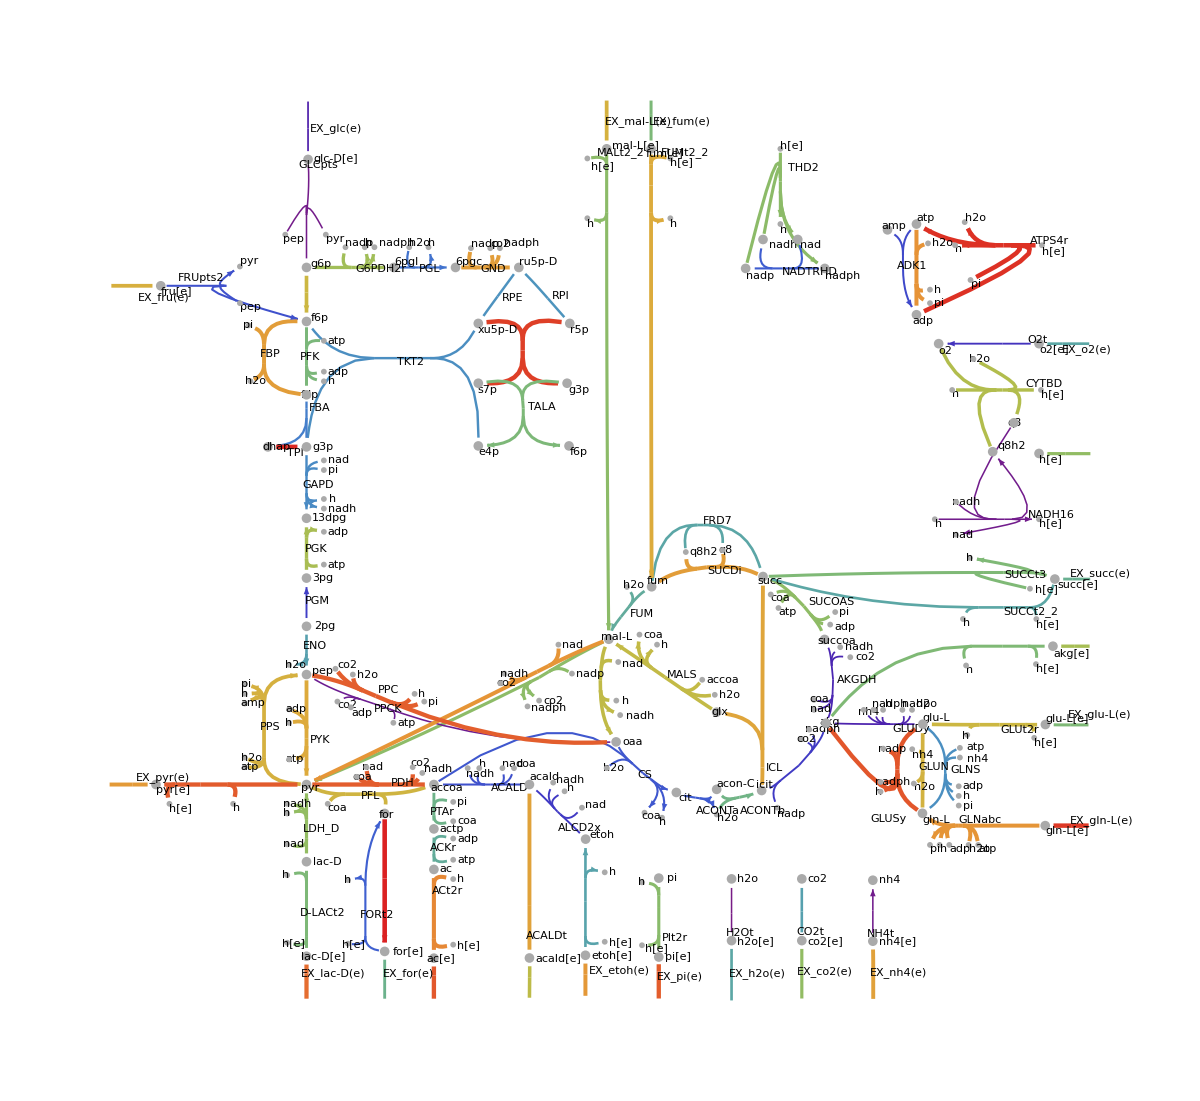

```mathematica
SetDirectory[NotebookDirectory[]];
{cmpdPos,rxnPos,textPos}=importBIGGmap["/Users/niko/work/Code/MathematicaRepo/MASSToolbox/Models/EcoliCoreMap.svg"];
fakeData=#->RandomReal[{-1,1}]&/@rxnPos[[All,1]];
drawPathway[cmpdPos,rxnPos,Flatten@textPos,ImageSize->1200,"TextStyle"->{FontFamily->"Arial",FontSize->Scaled[0.004]},ReactionStyle->{"DefaultStyle"->{Thickness[0.001],GrayLevel[0.5]}},Boundary->False,ReactionData->fakeData]
```

### From SB2

```mathematica
glycolysis=ExampleData[{"MASSToolbox","Glycolysis"}];
ppp=ExampleData[{"MASSToolbox","PentosePhosphatePathway"}];
```

### Import the the iAB-238-RBC reconstruction and pick a selection of relevant reactions

Notes:
The Keq values in iAB-238 have been adjusted for is=0.25 and pH=7.3

```mathematica
SetDirectory[NotebookDirectory[]];
iABglyc=Import["../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz"];
iABppp=Import["../models/iAB-RBC-238/iAB-RBC-238-PentosePhosphatePathway.m.gz"];
iABsalvage=Import["../models/iAB-RBC-238/iAB-RBC-238-NucleotideSalvagePathway.m.gz"];
SetDirectory[NotebookDirectory[]];
iAB=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
Select[iAB["Reactions"],MemberQ[getSubstrates@#,m["prpp","c"],∞]&]
Select[iAB["Reactions"],MemberQ[getSubstrates@#,m["gly",_],∞]&]
Select[iAB["Reactions"],MemberQ[getSubstrates@#,m["na1","e"],∞]&]
Select[iAB["Reactions"],MemberQ[getSubstrates@#,m["cl","e"],∞]&]
Select[iAB["Reactions"],MemberQ[getSubstrates@#,m["na1","e"],∞]&]
Select[iAB["Reactions"],MemberQ[getSubstrates@#,m["k","e"],∞]&]
```

{(ade^c+prpp^c→amp^c+ppi^c)^ADPT,(gua^c+prpp^c→gmp^c+ppi^c)^GUAPRT,(hxan^c+prpp^c→imp^c+ppi^c)^HXPRT}

{(cl^e+gly^e+2 na1^e⇌cl^c+gly^c+2 na1^c)^(GLYt7(211)r),(atp^c+glucys^c+gly^c→adp^c+gthrd^c+h^c+pi^c)^GTHS}

{(na1^e⇌∅)^(EX_na1(e)),((ala-L)^e+na1^e⇌(ala-L)^c+na1^c)^ALAt4,(chol^e+na1^e⇌chol^c+na1^c)^CHOLt4,((gln-L)^e+na1^e→(gln-L)^c+na1^c)^GLNt4,(cl^e+gly^e+2 na1^e⇌cl^c+gly^c+2 na1^c)^(GLYt7(211)r),(na1^e⇌na1^c)^NAt}

{(cl^e⇌∅)^(EX_cl(e)),(cl^e+gly^e+2 na1^e⇌cl^c+gly^c+2 na1^c)^(GLYt7(211)r),(cl^e+k^e⇌cl^c+k^c)^KCCt}

{(na1^e⇌∅)^(EX_na1(e)),((ala-L)^e+na1^e⇌(ala-L)^c+na1^c)^ALAt4,(chol^e+na1^e⇌chol^c+na1^c)^CHOLt4,((gln-L)^e+na1^e→(gln-L)^c+na1^c)^GLNt4,(cl^e+gly^e+2 na1^e⇌cl^c+gly^c+2 na1^c)^(GLYt7(211)r),(na1^e⇌na1^c)^NAt}

{(k^e⇌∅)^(EX_k(e)),(cl^e+k^e⇌cl^c+k^c)^KCCt,(atp^c+h2o^c+2 k^e+3 na1^c→adp^c+h^c+2 k^c+3 na1^e+pi^c)^NaKt}

```mathematica
"ADK1"/.iAB
"ADNK1"/.iAB
```

{(amp^c+atp^c⇌2 adp^c)^ADK1,Volume_c k_ADK1^⟶ (-((adp^c[t])^2)/K_ADK1+amp^c[t] atp^c[t])}

{(adn^c+atp^c→adp^c+amp^c+h^c)^ADNK1,Volume_c k_ADNK1^⟶ adn^c[t] atp^c[t]}

```mathematica
Sort[getID/@iAB["Fluxes"]]
```

{2KMBTA,3MOXTYRESSte,4PYRDX,5AOPt2,ACALDt,ACGAM2E,ACGAMK,ACNAM9PL,ACNAMPH,ACNAMt2,ACNMLr,ACP1(FMN),ACt2r,ADA,ADEt,ADK1,ADMDC,ADNCYC,ADNK1,ADNt,ADPT,ADRNLtu,AGDC,AGPAT1_16_0_16_0,AGPAT1_16_0_18_1,AGPAT1_16_0_18_2,AGPAT1_18_1_18_1,AGPAT1_18_1_18_2,AGPAT1_18_2_16_0,AGPAT1_18_2_18_1,AHC,ALAt4,ALDD2x,AMANK,AMPDA,AP4AH1,ARD1_hs,ARGN,ARGt5r,ARS_hs,ASCBt,BANDMT,BILGLCURt,BILIRBU,BILIRED,C160CPT1,C160CPT2rbc,C181CPT1,C181CPT2rbc,CA2t,CAATPS,CAMPt,CAT,CDIPTr_16_0_16_0,CDIPTr_16_0_18_1,CDIPTr_16_0_18_2,CDIPTr_18_1_18_1,CDIPTr_18_1_18_2,CDIPTr_18_2_16_0,CDIPTr_18_2_18_1,CDS_16_0_16_0,CDS_16_0_18_1,CDS_16_0_18_2,CDS_18_1_18_1,CDS_18_1_18_2,CDS_18_2_16_0,CDS_18_2_18_1,CEPTC_16_0_16_0,CEPTC_16_0_18_1,CEPTC_16_0_18_2,CEPTC_18_1_18_1,CEPTC_18_1_18_2,CEPTC_18_2_16_0,CEPTC_18_2_18_1,CEPTE_16_0_16_0,CEPTE_16_0_18_1,CEPTE_16_0_18_2,CEPTE_18_1_18_1,CEPTE_18_1_18_2,CEPTE_18_2_16_0,CEPTE_18_2_18_1,CGMPt,CHLP,CHLPCTD,CHOLK,CHOLt4,CO2t,COt,CPPPGO,CYStec,CYTK1,DAGK_hs_16_0_16_0,DAGK_hs_16_0_18_1,DAGK_hs_16_0_18_2,DAGK_hs_18_1_18_1,DAGK_hs_18_1_18_2,DAGK_hs_18_2_16_0,DAGK_hs_18_2_18_1,DGULND,DHAAt1r,D-LACt2,DM_nadh,DOPAMT,DOPAtu,DPGase,DPGM,ENO,ETHAK,ETHAt,ETHP,EX_35cgmp(e),EX_3moxtyr(e),EX_4pyrdx(e),EX_5aop(e),EX_acald(e),EX_ac(e),EX_acnam(e),EX_ade(e),EX_adn(e),EX_adrnl(e),EX_ala-L(e),EX_arg-L(e),EX_ascb-L(e),EX_bilglcur(e),EX_ca2(e),EX_camp(e),EX_chol(e),EX_cl(e),EX_co2(e),EX_co(e),EX_cys-L(e),EX_dhdascb(e),EX_dopa(e),EX_etha(e),EX_fe2(e),EX_fru(e),EX_fum(e),EX_gal(e),EX_gam(e),EX_glc(e),EX_gln-L(e),EX_gluala(e),EX_glyc(e),EX_gly(e),EX_gthox(e),EX_h2o2(e),EX_h2o(e),EX_hco3(e),EX_hcyst-L(e),EX_hdca(e),EX_h(e),EX_hxan(e),EX_ins(e),EX_k(e),EX_lac-D(e),EX_lac-L(e),EX_leuktrA4(e),EX_leuktrB4(e),EX_lnlc(e),EX_mal-L(e),EX_man(e),EX_mepi(e),EX_met-L(e),EX_na1(e),EX_nac(e),EX_ncam(e),EX_nh4(e),EX_normete-L(e),EX_nrpphr(e),EX_o2(e),EX_ocdcea(e),EX_orot(e),EX_phe-L(e),EX_pi(e),EX_ptrc(e),EX_pydam(e),EX_pydx(e),EX_pydxn(e),EX_pyr(e),EX_ribflv(e),EX_spmd(e),EX_sprm(e),EX_thm(e),EX_thmmp(e),EX_urea(e),EX_uri(e),FACOAL160,FACOAL181,FACOAL1821,FADDP,FBA,FBP26,FCLT,FE2t1,FMNAT,FRUt1r,FUM,FUMtr,G6PDA,G6PDH2r,GALK,GALOR,GALT,GALt1r,GALU,GAMt1r,GAPD,GGLUCT,GK1,GLCt1r,GLNS,GLNt4,GLUCYS,GLYCt,GLYK,GLYOX,GLYt7(211)r,GMPR,GMPS2,GND,GPAM_hs_16_0,GPAM_hs_18_1,GPAM_hs_18_2,GPDDA1,GTHDH,GTHO,GTHOXti2,GTHP,GTHS,GUACYC,GUAPRT,GULN3D,GULND,H2O2t,H2Ot,HCO3_CLt,HCO3E,HCYSte,HDCAtr,HEX1,HEX10,HEX4,HEX7,HMBS,HOXG,Ht,HXPRT,HYXNt,ICDHy,IMPD,INSt,KCCt,LDH_L,LEUKTRA4t,LEUKTRB4t,LGTHL,L-LACt2r,LNLCCPT1,LNLCCPT2rbc,LNLCt,LPASE_16_0,LPASE_18_1,LPASE_18_2,LTA4H,MALt,MAN6PI,MANt1r,MDH,MDRPD,ME2,MEPIVESSte,METAT,METtec,MGSA,MI1345PP,MI145PK,MI145PP,MI1PP,MI1PS,MTAP,MTRI,NACt,NADK,NADPN,NADS2,NaKt,NAt,NCAMt,NDPK1,NDPK2,NDPK3,NH4t3r,NICRNS,NMNATr,NNATr,NORMETEVESSte,NP1,NRPPHRtu,NT5C,NTD11,NTD2,NTD5_a,NTD7,NTD9,O2t,OCDCEAtr,OMPDC,OPAHir,ORNDC,OROATP,ORPT,PDE1,PDX5PO,PDXPP,PETHCT,PFK,PFK26,PGI,PGK,PGL,PGM,PGMT,PHETA1,PHEtec,PI45P5P_16_0_16_0,PI45P5P_16_0_18_1,PI45P5P_16_0_18_2,PI45P5P_18_1_18_1,PI45P5P_18_1_18_2,PI45P5P_18_2_16_0,PI45P5P_18_2_18_1,PI45PLC_16_0_16_0,PI45PLC_16_0_18_1,PI45PLC_16_0_18_2,PI45PLC_18_1_18_1,PI45PLC_18_1_18_2,PI45PLC_18_2_16_0,PI45PLC_18_2_18_1,PI4P5K_16_0_16_0,PI4P5K_16_0_18_1,PI4P5K_16_0_18_2,PI4P5K_18_1_18_1,PI4P5K_18_1_18_2,PI4P5K_18_2_16_0,PI4P5K_18_2_18_1,PI4PLC_16_0_16_0,PI4PLC_16_0_18_1,PI4PLC_16_0_18_2,PI4PLC_18_1_18_1,PI4PLC_18_1_18_2,PI4PLC_18_2_16_0,PI4PLC_18_2_18_1,PI4PP_16_0_16_0,PI4PP_16_0_18_1,PI4PP_16_0_18_2,PI4PP_18_1_18_1,PI4PP_18_1_18_2,PI4PP_18_2_16_0,PI4PP_18_2_18_1,PIK4_16_0_16_0,PIK4_16_0_18_1,PIK4_16_0_18_2,PIK4_18_1_18_1,PIK4_18_1_18_2,PIK4_18_2_16_0,PIK4_18_2_18_1,PIPLC_16_0_16_0,PIPLC_16_0_18_1,PIPLC_16_0_18_2,PIPLC_18_1_18_1,PIPLC_18_1_18_2,PIPLC_18_2_16_0,PIPLC_18_2_18_1,PIt,PLA2_2_16_0_16_0,PLA2_2_16_0_18_1,PLA2_2_16_0_18_2,PLA2_2_18_1_18_1,PLA2_2_18_1_18_2,PLA2_2_18_2_16_0,PLA2_2_18_2_18_1,PMANM,PNP,PPA,PPAP_16_0_16_0,PPAP_16_0_18_1,PPAP_16_0_18_2,PPAP_18_1_18_1,PPAP_18_1_18_2,PPAP_18_2_16_0,PPAP_18_2_18_1,PPBNGS,PPM,PPPGO,PRPPS,PTRCt,PUNP1,PUNP3,PUNP5,PYAM5PO,PYDAMK,PYDAMtr,PYDXDH,PYDXK,PYDXNK,PYDXNtr,PYDXPP,PYDXtr,PYK,PYRt2r,RBFK,RIBFLVt3,RIBFLVt3o,RNMK,RPE,RPI,SALMCOM,SALMCOM2,SBTD_D2,SBTR,sink_adprbp(c),sink_akg(c),sink_band(c),sink_bandmt(c),sink_for(c),sink_mi1345p(c),sink_mi134p(c),sink_mi145p(c),sink_mi14p(c),sink_pchol_hs_16_0_16_0(c),sink_pchol_hs_16_0_18_1(c),sink_pchol_hs_16_0_18_2(c),sink_pchol_hs_18_1_18_1(c),sink_pchol_hs_18_1_18_2(c),sink_pchol_hs_18_2_16_0(c),sink_pchol_hs_18_2_18_1(c),sink_pe_hs_16_0_16_0(c),sink_pe_hs_16_0_18_1(c),sink_pe_hs_16_0_18_2(c),sink_pe_hs_18_1_18_1(c),sink_pe_hs_18_1_18_2(c),sink_pe_hs_18_2_16_0(c),sink_pe_hs_18_2_18_1(c),SPMDt,SPMS,SPRMS,SPRMt2r,TALA,TDP,THMMPtrbc,THMTP,THMtrbc,TKT1,TKT2,TMDPK,TMDPPK,TPI,UDPG4E,UDPGD,UDPGNP,UGLT,UMPK,UPP3S,UPPDC1,UREAt,URIt,XYLK,XYLTD_Dr,XYLUR}

```mathematica
rxnsOfInterest={"GLCt1r","ENO","FBA","GAPD","HEX1","LDH_L","PFK","PGI","PGK","PGM","PYK","TPI","G6PDH2r","GND","GTHO","GTHP","GTHOXti2","PGL","RPE","RPI","TALA","TKT1","TKT2","ADA","ADNK1","ADPT","AMPDA","NTD11","NTD7","PPM","PRPPS","PUNP5","HXPRT","DPGM","DPGase","L-LACt2r","ADEt","ADNt","INSt","PYRt2r","GLUCYS","GTHS","PIt","Ht","H2Ot","CO2t","NH4t3r","H2O2t","HYXNt","CYStec","PPA","GLYt7(211)r","KCCt","NAt","NaKt"};
```

### Construction of the sub-model

Construct sub-model from reaction selection

```mathematica
rbc=subModel[iAB,rxnsOfInterest];
setUnitChecking[rbc,True]
(*Adjust missing units for parameters*)
Quiet@updateParameters[rbc,{}];
```

Replace ATP and ADP by their Mg complexed counterparts

```mathematica
rbc=rbc/.{atp^c->{{Mg^c, atp^c}},adp^c->{{Mg^c, adp^c}},amp^c->{{Mg^c, amp^c}}};
```

Add a few important reactions that are not present in iAB-RBC-238

```mathematica
bigg2inchi[[1]]
```

(2pg)^_→InChI[InChI=1S/C3H7O7P/c4-1-2(3(5)6)10-11(7,8)9/h2,4H,1H2,(H,5,6)(H2,7,8,9)/t2-/m1/s1]

```mathematica
FullForm[(2pg)^_->InChI["InChI=1S/C3H7O7P/c4-1-2(3(5)6)10-11(7,8)9/h2,4H,1H2,(H,5,6)(H2,7,8,9)/t2-/m1/s1"]]
```

Rule[metabolite["2pg",Blank[]],InChI["InChI=1S/C3H7O7P/c4-1-2(3(5)6)10-11(7,8)9/h2,4H,1H2,(H,5,6)(H2,7,8,9)/t2-/m1/s1"]]

```mathematica
rbcInChI=FilterRules[bigg2inchi,m[#[[1]],_]&/@rbc["Species"]];
```

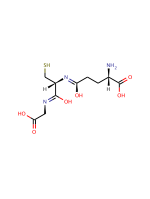

```mathematica
drawCompound[m["gthrd","c"]/.rbcInChI]
```

```mathematica
notInRecon={Overscript[{{Mg^c, atp^c}}+amp^c⇌{{Mg^c, adp^c}}+adp^c, ADK1_Mg],Overscript[atp^c+Mg^c⇌{{Mg^c, atp^c}}, Mg+ATP],Overscript[adp^c+Mg^c⇌{{Mg^c, adp^c}}, Mg+ADP],Overscript[amp^c+Mg^c⇌{{Mg^c, amp^c}}, Mg+AMP],Overscript[{{Mg^c, atp^c}}+3 h^c+h2o^c⇌{{Mg^c, adp^c}}+4 h^c+pi^c, ATPaseI_Mg]};
```

```mathematica
#->0&/@getID/@rbc["Reactions"]
```

{ADA→0,ADEt→0,ADNK1→0,ADNt→0,ADPT→0,AMPDA→0,CO2t→0,CYStec→0,DPGM→0,DPGase→0,ENO→0,FBA→0,G6PDH2r→0,GAPD→0,GLCt1r→0,GLUCYS→0,GLYt7(211)r→0,GND→0,GTHO→0,GTHOXti2→0,GTHP→0,GTHS→0,H2O2t→0,H2Ot→0,HEX1→0,HXPRT→0,HYXNt→0,Ht→0,INSt→0,KCCt→0,L-LACt2r→0,LDH_L→0,NAt→0,NH4t3r→0,NTD11→0,NTD7→0,NaKt→0,PFK→0,PGI→0,PGK→0,PGL→0,PGM→0,PIt→0,PPA→0,PPM→0,PRPPS→0,PUNP5→0,PYK→0,PYRt2r→0,RPE→0,RPI→0,TALA→0,TKT1→0,TKT2→0,TPI→0}

```mathematica
Options[drawPathway]
```

{Boundary→True,ReactionData→{},MetaboliteData→{},ColorFunction→ColorDataFunction[{0,1},-Graphics-],MinSize→0.005,MaxSize→0.01,MinThickness→0.001,MaxThickness→0.003,Directed→True,TextStyle→{FontFamily→Arial,FontSize→Scaled[0.008]},MetaboliteStyle→{Style→{},DefaultStyle→{RGBColor[0.666667,0.666667,0.666667],PointSize[0.01]},Tooltips→True,Hyperlinks→False},ReactionStyle→{AbsentStyle→{Dashing[{0,Small}],Thickness[0.001],RGBColor[0.666667,0.666667,0.666667]},DefaultStyle→{Thickness[0.002],GrayLevel[0.5]},Tooltips→True,Style→{},Directed→True,Arrowheads→0.01,Hyperlinks→False},ImageSize→350}

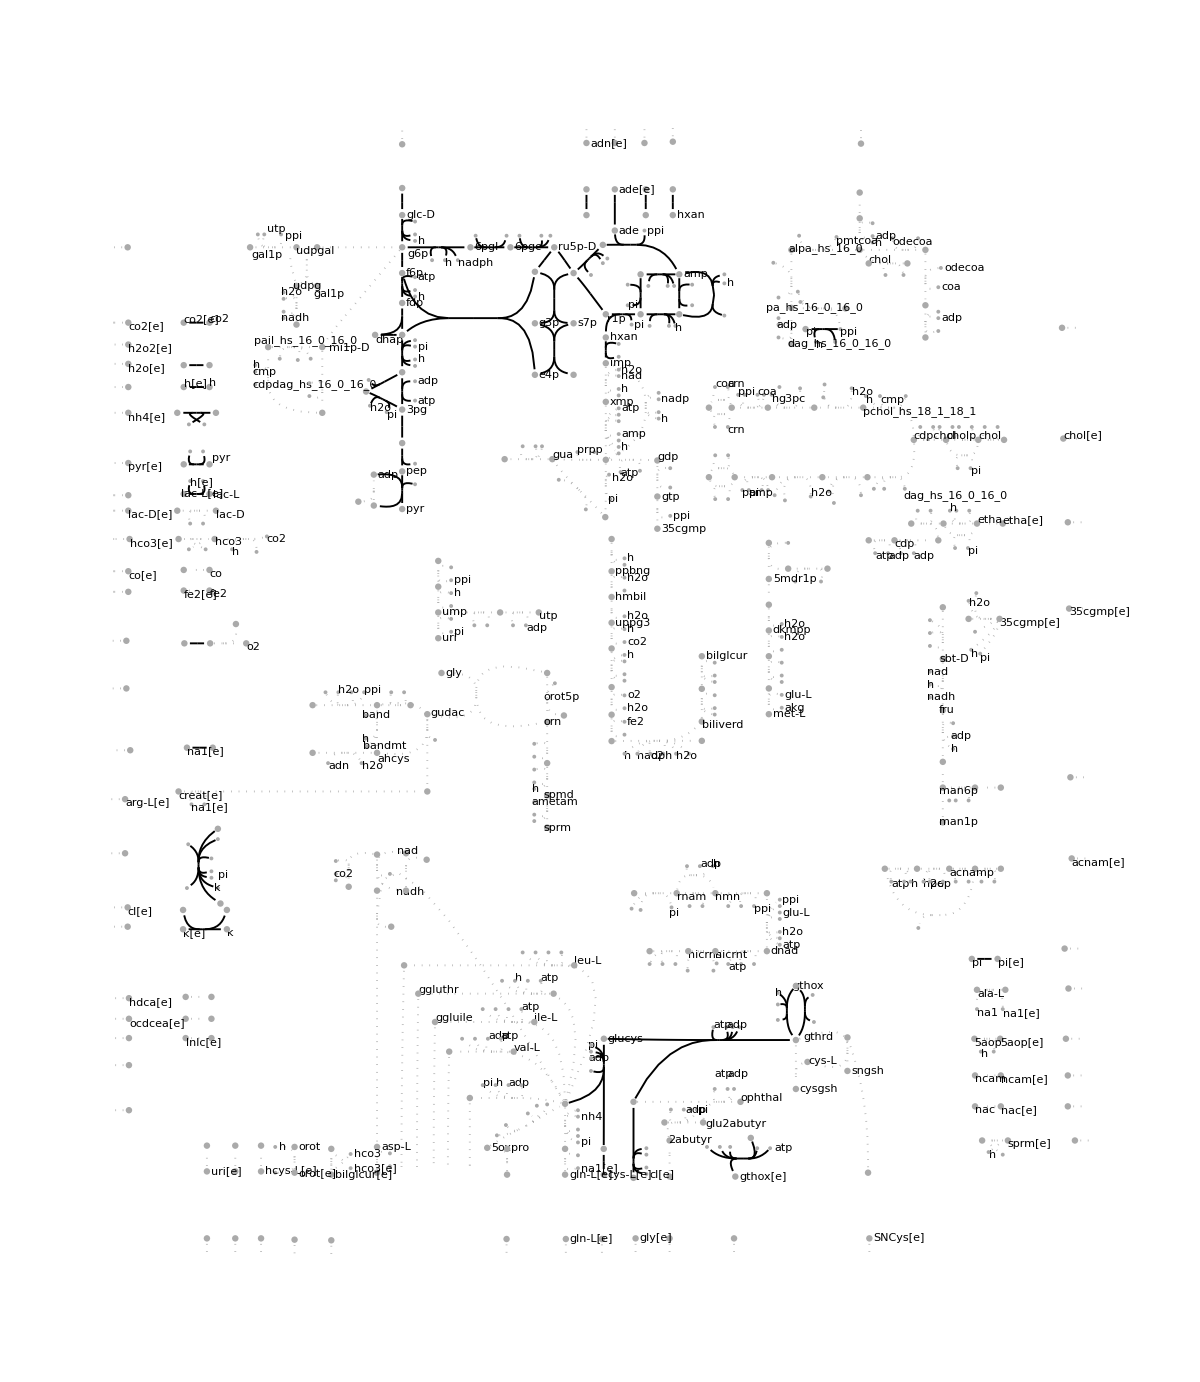

```mathematica
SetDirectory[NotebookDirectory[]];
{cmpdPos,rxnPos,textPos}=importBIGGmap["../data/iAB-RBC-238/iAB-RBC-283-ReducedMap.svg"];
drawPathway[cmpdPos,rxnPos,Flatten@textPos,ImageSize->1200,"TextStyle"->{FontFamily->"Arial",FontSize->Scaled[0.004]},ReactionStyle->{"DefaultStyle"->{Thickness[0.001],GrayLevel[0.5]}},ColorFunction->(Black&),Boundary->False,ReactionData->(#->0&/@getID/@rbc["Reactions"])]
```

We have to provide a few missing equilibrium constants. The Mg complex forming constants have been obtained from Joshi 1990. Experimentally determined values from
Storer, A. C., & Cornish-Bowden, A. (1976). Concentration of MgATP2- and other ions in solution. Calculation of the true concentrations of species present in mixtures of associating ions. The Biochemical Journal, 159(1), 1–5.
should probably used instead.

```mathematica
keqNotInRecon={Keq["ATPaseI_Mg"]->6.3*^6(*eQuilibrator*),Keq["ADK1_Mg"]->Keq["ADK1"],Keq["Mg+ATP"]->1/(0.081Millimole Liter^-1),Keq["Mg+ADP"]->1/(0.81Millimole Liter^-1),Keq["Mg+AMP"]->1/(22.2Millimole Liter^-1)}/.iAB;
```

```mathematica
rbc=addReactions[rbc,notInRecon];
```

Annotate currency metabolites for pathway visualizations.

```mathematica
updateParameters[rbc,keqNotInRecon]
```

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed.

Add exchange reactions

```mathematica
externalSpecies=Select[rbc["Species"],getCompartment[#]=="e"&]
boundaryConditions={m["glu-L","c"],m["amp","c"]};
```

{ade^e,adn^e,co2^e,(cys-L)^e,(glc-D)^e,gthox^e,h^e,h2o^e,h2o2^e,hxan^e,(lac-L)^e,nh4^e,pi^e,pyr^e,cl^e,gly^e,ins^e,k^e,na1^e}

```mathematica
rbc=addExchanges[rbc,externalSpecies];
rbc=addSinks[rbc,boundaryConditions];
```

```mathematica
TableForm[rbc["Reactions"]]
```

(adn^c+h^c+h2o^c→ins^c+nh4^c)^ADA
(ade^e⇌ade^c)^ADEt
(Mg^c | atp^c+adn^c→Mg^c | adp^c+Mg^c | amp^c+h^c)^ADNK1
(adn^e⇌adn^c)^ADNt
(ade^c+prpp^c→Mg^c | amp^c+ppi^c)^ADPT
(Mg^c | amp^c+h^c+h2o^c→imp^c+nh4^c)^AMPDA
(co2^e⇌co2^c)^CO2t
((cys-L)^e⇌(cys-L)^c)^CYStec
((13dpg)^c⇌(23dpg)^c+h^c)^DPGM
((23dpg)^c+h2o^c→(3pg)^c+pi^c)^DPGase
((2pg)^c⇌h2o^c+pep^c)^ENO
(fdp^c⇌dhap^c+g3p^c)^FBA
(g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^G6PDH2r
(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD
((glc-D)^e⇌(glc-D)^c)^GLCt1r
(Mg^c | atp^c+(cys-L)^c+(glu-L)^c→Mg^c | adp^c+glucys^c+h^c+pi^c)^GLUCYS
(cl^e+gly^e+2 na1^e⇌cl^c+gly^c+2 na1^c)^(GLYt7(211)r)
((6pgc)^c+nadp^c→co2^c+nadph^c+(ru5p-D)^c)^GND
(gthox^c+h^c+nadph^c→2 gthrd^c+nadp^c)^GTHO
(Mg^c | atp^c+gthox^c+h2o^c→Mg^c | adp^c+gthox^e+h^c+pi^c)^GTHOXti2
(2 gthrd^c+h2o2^c→gthox^c+2 h2o^c)^GTHP
(Mg^c | atp^c+glucys^c+gly^c→Mg^c | adp^c+gthrd^c+h^c+pi^c)^GTHS
(h2o2^e⇌h2o2^c)^H2O2t
(h2o^e⇌h2o^c)^H2Ot
(Mg^c | atp^c+(glc-D)^c→Mg^c | adp^c+g6p^c+h^c)^HEX1
(hxan^c+prpp^c→imp^c+ppi^c)^HXPRT
(hxan^e⇌hxan^c)^HYXNt
(h^c⇌h^e)^Ht
(ins^e⇌ins^c)^INSt
(cl^e+k^e⇌cl^c+k^c)^KCCt
(h^e+(lac-L)^e⇌h^c+(lac-L)^c)^(L-LACt2r)
((lac-L)^c+nad^c⇌h^c+nadh^c+pyr^c)^LDH_L
(na1^e⇌na1^c)^NAt
(h^e+nh4^c⇌h^c+nh4^e)^NH4t3r
(h2o^c+imp^c→ins^c+pi^c)^NTD11
(Mg^c | amp^c+h2o^c→adn^c+pi^c)^NTD7
(Mg^c | atp^c+h2o^c+2 k^e+3 na1^c→Mg^c | adp^c+h^c+2 k^c+3 na1^e+pi^c)^NaKt
(Mg^c | atp^c+f6p^c→Mg^c | adp^c+fdp^c+h^c)^PFK
(g6p^c⇌f6p^c)^PGI
(Mg^c | atp^c+(3pg)^c⇌Mg^c | adp^c+(13dpg)^c)^PGK
((6pgl)^c+h2o^c→(6pgc)^c+h^c)^PGL
((2pg)^c⇌(3pg)^c)^PGM
(pi^c⇌pi^e)^PIt
(h2o^c+ppi^c→h^c+2 pi^c)^PPA
(r1p^c⇌r5p^c)^PPM
(Mg^c | atp^c+r5p^c⇌Mg^c | amp^c+h^c+prpp^c)^PRPPS
(ins^c+pi^c⇌hxan^c+r1p^c)^PUNP5
(Mg^c | adp^c+h^c+pep^c→Mg^c | atp^c+pyr^c)^PYK
(h^e+pyr^e⇌h^c+pyr^c)^PYRt2r
((ru5p-D)^c⇌(xu5p-D)^c)^RPE
(r5p^c⇌(ru5p-D)^c)^RPI
(g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA
(r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1
(e4p^c+(xu5p-D)^c⇌f6p^c+g3p^c)^TKT2
(dhap^c⇌g3p^c)^TPI
(Mg^c | atp^c+amp^c⇌Mg^c | adp^c+adp^c)^ADK1_Mg
(atp^c+Mg^c⇌Mg^c | atp^c)^(Mg+ATP)
(adp^c+Mg^c⇌Mg^c | adp^c)^(Mg+ADP)
(amp^c+Mg^c⇌Mg^c | amp^c)^(Mg+AMP)
(Mg^c | atp^c+h2o^c⇌Mg^c | adp^c+4 h^c+pi^c)^ATPaseI_Mg
(ade^e⇌∅)^EX_ade[e]
(adn^e⇌∅)^EX_adn[e]
(co2^e⇌∅)^EX_co2[e]
((cys-L)^e⇌∅)^(EX_cys-L[e])
((glc-D)^e⇌∅)^(EX_glc-D[e])
(gthox^e⇌∅)^EX_gthox[e]
(h^e⇌∅)^EX_h[e]
(h2o^e⇌∅)^EX_h2o[e]
(h2o2^e⇌∅)^EX_h2o2[e]
(hxan^e⇌∅)^EX_hxan[e]
((lac-L)^e⇌∅)^(EX_lac-L[e])
(nh4^e⇌∅)^EX_nh4[e]
(pi^e⇌∅)^EX_pi[e]
(pyr^e⇌∅)^EX_pyr[e]
(cl^e⇌∅)^EX_cl[e]
(gly^e⇌∅)^EX_gly[e]
(ins^e⇌∅)^EX_ins[e]
(k^e⇌∅)^EX_k[e]
(na1^e⇌∅)^EX_na1[e]
((glu-L)^c⇌∅)^(Sink_glu-L[c])
(amp^c⇌∅)^Sink_amp[c]

```mathematica
currAnnot=annotateCurrencyMetabolites[rbc["Reactions"],{"ADA"->{h^c,h2o^c,nh4^c},"ADEt"->{},"ADNK1"->{{{Mg^c, atp^c}},{{Mg^c, adp^c}},h^c},"ADNt"->{},"ADPT"->{ppi^c},"AMPDA"->{h^c,h2o^c,nh4^c},"CO2t"->{},"CYStec"->{},"DPGM"->{h^c},"DPGase"->{h2o^c,pi^c},"ENO"->{h2o^c},"FBA"->{},"G6PDH2r"->{nadp^c,h^c,nadph^c},"GAPD"->{nad^c,pi^c,h^c,nadh^c},"GLCt1r"->{},"GLUCYS"->{{{Mg^c, atp^c}},{{Mg^c, adp^c}},h^c,pi^c},"GND"->{nadp^c,co2^c,nadph^c},"GTHO"->{h^c,nadph^c,nadp^c},"GTHOXti2"->{{{Mg^c, atp^c}},h2o^c,{{Mg^c, adp^c}},h^c,pi^c},"GTHP"->{h2o^c},"GTHS"->{{{Mg^c, atp^c}},{{Mg^c, adp^c}},h^c,pi^c},"H2O2t"->{},"H2Ot"->{},"HEX1"->{{{Mg^c, atp^c}},{{Mg^c, adp^c}},h^c},"HXPRT"->{ppi^c},"HYXNt"->{},"Ht"->{},"INSt"->{},"L-LACt2r"->{h^e,h^c},"LDH_L"->{nad^c,h^c,nadh^c},"NH4t3r"->{h^e,h^c},"NTD11"->{h2o^c,pi^c},"NTD7"->{h2o^c,pi^c},"PFK"->{{{Mg^c, atp^c}},{{Mg^c, adp^c}},h^c},"PGI"->{},"PGK"->{{{Mg^c, atp^c}},{{Mg^c, adp^c}}},"PGL"->{h2o^c,h^c},"PGM"->{},"PIt"->{},"PPA"->{h2o^c,h^c},"PPM"->{},"PRPPS"->{{{Mg^c, atp^c}},h^c,amp^c},"PUNP5"->{pi^c},"PYK"->{{{Mg^c, adp^c}},h^c,{{Mg^c, atp^c}}},"PYRt2r"->{h^e,h^c},"RPE"->{},"RPI"->{},"TALA"->{},"TKT1"->{},"TKT2"->{},"TPI"->{},"ADK1_Mg"->{},"Mg+ATP"->{},"Mg+ADP"->{},"Mg+AMP"->{},"ATPaseI_Mg"->{h2o^c,h^c,pi^c},"EX_ade[e]"->{},"EX_adn[e]"->{},"EX_co2[e]"->{},"EX_cys-L[e]"->{},"EX_glc-D[e]"->{},"EX_gthox[e]"->{},"EX_h[e]"->{},"EX_h2o[e]"->{},"EX_h2o2[e]"->{},"EX_hxan[e]"->{},"EX_lac-L[e]"->{},"EX_pi[e]"->{},"EX_pyr[e]"->{},"EX_ins[e]"->{},"EX_nh4[e]"->{},"Sink_glu-L[c]"->{},"Sink_amp[c]"->{},"GLYt7(211)r"->{},"EX_cl[e]"->{},"EX_gly[e]"->{},"EX_na1[e]"->{},"KCCt"->{},"NAt"->{},"NaKt"->{{{Mg^c, atp^c}},h2o^c,{{Mg^c, adp^c}},h^c,pi^c},"EX_k[e]"->{}}];
```

```mathematica
bip=model2bipartite[rbc,DeletionRules->currAnnot];
```

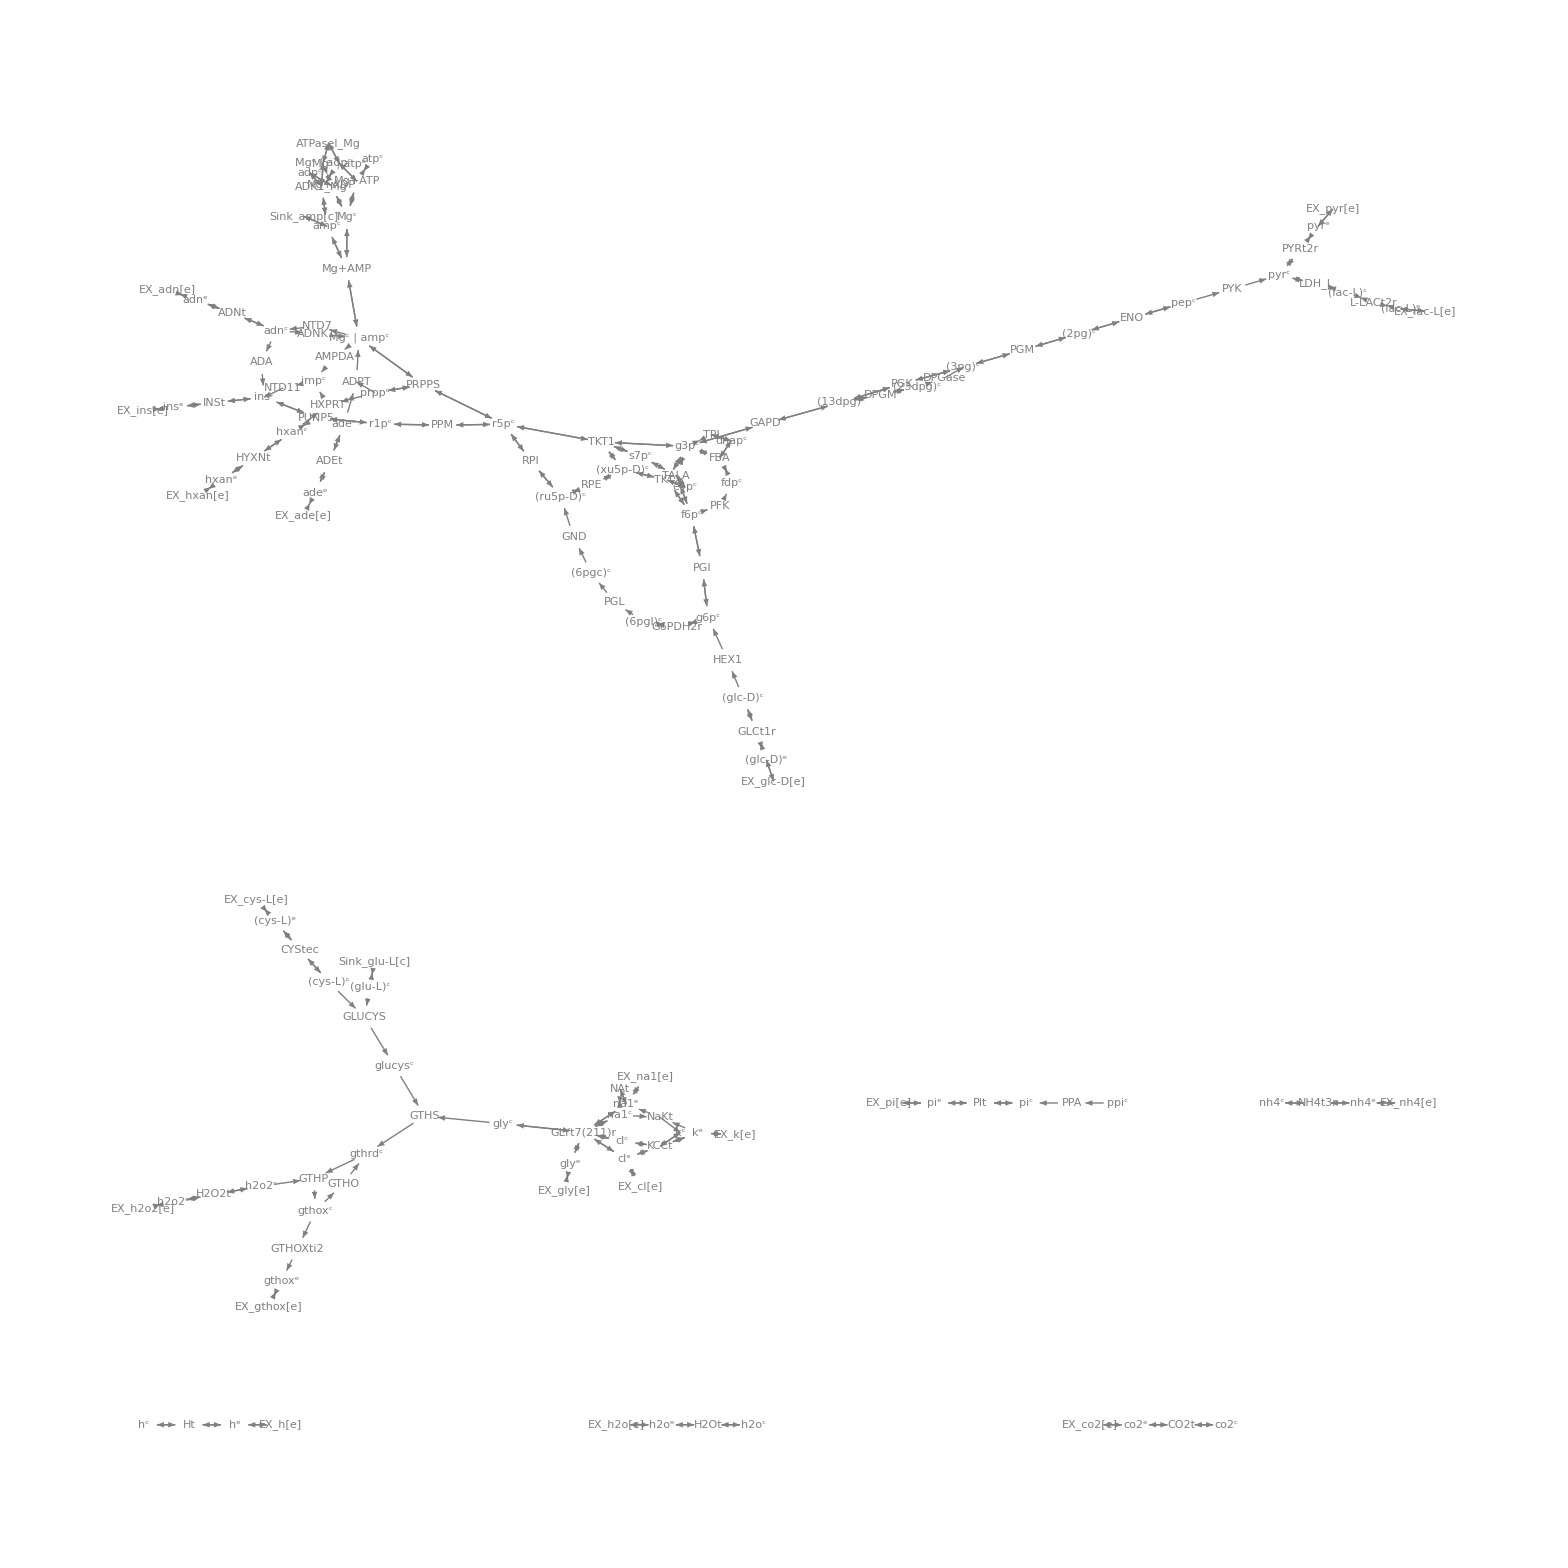

```mathematica
visualizePathways[bip,PlotFunction->GraphPlot,ImageSize->2200]/.(getID[#]->Tooltip[getID[#],#]&/@rbc["Reactions"])
```

```mathematica
Complement[rbc["Fluxes"],Union[Cases[NullSpace[rbc].rbc["Fluxes"],_v,∞]]]
```

{v_EX_cl[e],v_EX_k[e],v_EX_na1[e],v_EX_pi[e],v_EX_pyr[e],v_(Mg+ATP),v_PIt,v_PYRt2r,v_Sink_amp[c]}

### Determine steady-state fluxes

```mathematica
Select[#,#[[2]]≠0&]&/@Chop@fba[rbc,Subscript[v, PYRt2r],getID[#]->{-10,10}&/@getExchanges[rbc],Solver->DualLinearProgramming]
Select[#,#[[2]]≠0&]&/@Chop@fba[rbc,v["L-LACt2r"],getID[#]->{-10,10}&/@getExchanges[rbc],Solver->DualLinearProgramming]
```

{{v_ADEt→3.33333,v_ADNt→-3.33333,v_ADPT→3.33333,v_CYStec→5.33333,v_ENO→10.,v_FBA→4.,v_GAPD→10.,v_GLUCYS→5.33333,v_(GLYt7(211)r)→5.33333,v_GTHOXti2→2.66667,v_GTHP→2.66667,v_GTHS→5.33333,v_H2O2t→2.66667,v_H2Ot→-10.,v_HYXNt→-9.33333,v_Ht→-20.,v_INSt→9.33333,v_KCCt→-5.33333,v_(L-LACt2r)→-10.,v_LDH_L→-10.,v_NAt→-2.66667,v_NTD7→3.33333,v_NaKt→2.66667,v_PFK→4.,v_PGK→-10.,v_PGM→-10.,v_PPA→3.33333,v_PPM→9.33333,v_PRPPS→3.33333,v_PUNP5→9.33333,v_PYK→10.,v_RPE→4.,v_RPI→4.,v_TALA→2.,v_TKT1→2.,v_TKT2→2.,v_TPI→4.,v_ADK1_Mg→3.33333,v_(Mg+ADP)→3.33333,v_(Mg+AMP)→-3.33333,v_ATPaseI_Mg→-6.66667,v_EX_ade[e]→-3.33333,v_EX_adn[e]→3.33333,v_(EX_cys-L[e])→-5.33333,v_EX_gthox[e]→2.66667,v_EX_h[e]→-10.,v_EX_h2o[e]→10.,v_EX_h2o2[e]→-2.66667,v_EX_hxan[e]→9.33333,v_(EX_lac-L[e])→10.,v_EX_gly[e]→-5.33333,v_EX_ins[e]→-9.33333,v_(Sink_glu-L[c])→-5.33333},{(13dpg)^c→-1.,(23dpg)^c→-1.,(2pg)^c→-1.,(3pg)^c→-1.,nad^c→-1.,pep^c→-1.,pyr^c→-1.},{},{}}

{{v_CO2t→-2.22222,v_CYStec→0.37037,v_G6PDH2r→2.22222,v_GLCt1r→2.22222,v_GLUCYS→0.37037,v_(GLYt7(211)r)→0.37037,v_GND→2.22222,v_GTHO→4.44444,v_GTHOXti2→0.185185,v_GTHP→4.62963,v_GTHS→0.37037,v_H2O2t→4.62963,v_H2Ot→-10.,v_HEX1→2.22222,v_HYXNt→2.22222,v_Ht→-10.,v_INSt→-2.22222,v_KCCt→-0.37037,v_NAt→-0.185185,v_NaKt→0.185185,v_PGL→2.22222,v_PPM→-2.22222,v_PUNP5→-2.22222,v_RPI→-2.22222,v_ATPaseI_Mg→-3.33333,v_EX_co2[e]→2.22222,v_(EX_cys-L[e])→-0.37037,v_(EX_glc-D[e])→-2.22222,v_EX_gthox[e]→0.185185,v_EX_h[e]→-10.,v_EX_h2o[e]→10.,v_EX_h2o2[e]→-4.62963,v_EX_hxan[e]→-2.22222,v_EX_gly[e]→-0.37037,v_EX_ins[e]→2.22222,v_(Sink_glu-L[c])→-0.37037},{(13dpg)^c→1.,(23dpg)^c→1.,(2pg)^c→1.,(3pg)^c→1.,(lac-L)^c→-1.,nad^c→1.,pep^c→1.},{v_PYK→1.},{}}

```mathematica
Select[#,#[[2]]≠0&]&/@Chop@fba[rbc,Subscript[v, GTHS],getID[#]->{-20,20}&/@getExchanges[rbc],Solver->DualLinearProgramming]
```

{{v_ADA→10.,v_ADNt→10.,v_CYStec→14.,v_ENO→20.,v_FBA→8.,v_GAPD→20.,v_GLUCYS→14.,v_(GLYt7(211)r)→14.,v_GTHOXti2→7.,v_GTHP→7.,v_GTHS→14.,v_H2O2t→7.,v_H2Ot→-20.,v_HYXNt→-12.,v_Ht→-30.,v_INSt→2.,v_KCCt→-14.,v_(L-LACt2r)→-20.,v_LDH_L→-20.,v_NAt→-7.,v_NH4t3r→10.,v_NaKt→7.,v_PFK→8.,v_PGK→-20.,v_PGM→-20.,v_PPM→12.,v_PUNP5→12.,v_PYK→20.,v_RPE→8.,v_RPI→8.,v_TALA→4.,v_TKT1→4.,v_TKT2→4.,v_TPI→8.,v_ATPaseI_Mg→-10.,v_EX_adn[e]→-10.,v_(EX_cys-L[e])→-14.,v_EX_gthox[e]→7.,v_EX_h[e]→-20.,v_EX_h2o[e]→20.,v_EX_h2o2[e]→-7.,v_EX_hxan[e]→12.,v_(EX_lac-L[e])→20.,v_EX_nh4[e]→10.,v_EX_gly[e]→-14.,v_EX_ins[e]→-2.,v_(Sink_glu-L[c])→-14.},{(13dpg)^c→0.666667,(23dpg)^c→0.583333,(2pg)^c→0.25,(3pg)^c→0.25,(6pgc)^c→-0.158333,(6pgl)^c→0.00833333,Mg^c | adp^c→0.5,Mg^c | amp^c→0.0833333,Mg^c | atp^c→0.916667,cl^c→-0.125,dhap^c→0.133333,e4p^c→0.0666667,f6p^c→-0.0666667,fdp^c→0.266667,g3p^c→0.133333,g6p^c→-0.0666667,glucys^c→0.333333,gly^c→0.125,gthox^c→-0.25,h^c→0.0833333,h^e→0.0833333,h2o^c→-0.0833333,h2o^e→-0.0833333,imp^c→0.0833333,k^c→0.125,(lac-L)^c→-0.533333,(lac-L)^e→-0.533333,nad^c→0.616667,pep^c→0.333333,ppi^c→0.666667,prpp^c→0.75,s7p^c→-0.133333,gthrd^c→-0.208333,nadp^c→0.158333,adp^c→0.416667,Mg^c→0.0833333,atp^c→0.833333},{v_ADNK1→0.25,v_DPGase→0.25,v_GTHO→0.0916667,v_HEX1→0.4,v_PPA→0.5,v_EX_h[e]→0.0833333},{v_EX_h2o[e]→0.0833333,v_(EX_lac-L[e])→0.533333}}

```mathematica
Cases[Chop@fva[rbc,getID[#]->{-20,20}&/@getExchanges[rbc]],r_Rule/;r[[2]]=={0,0}]//TableForm
```

v_PIt→{0,0}
v_PYRt2r→{0,0}
v_(Mg+ATP)→{0,0}
v_EX_pi[e]→{0,0}
v_EX_pyr[e]→{0,0}
v_EX_cl[e]→{0,0}
v_EX_k[e]→{0,0}
v_EX_na1[e]→{0,0}
v_Sink_amp[c]→{0,0}

```mathematica
NullSpace[rbc]//Dimensions
```

{10,81}

```mathematica
knownFluxes={Subscript[v, HEX1]->1.44,Subscript[v, G6PDH2r]->0.147,Subscript[v, TKT1]->0.0486,Subscript[v, DPGM]->0.538,Subscript[v, ATPaseI_Mg]->2.24,Subscript[v, ADA]->0.01,Subscript[v, NTD7]->0.096,Subscript[v, AMPDA]->0.014};
steadyStateFluxes=#[[1]]->#[[2]] Millimole Hour^-1 Liter^-1&/@Chop@Solve[Join[Thread[0==rbc.rbc["Fluxes"]],Equal@@@knownFluxes]][[1]];
TraditionalForm[steadyStateFluxes//TableForm]
```

v_ADA→0.01 mmol h^-1 l^-1
v_ADEt→0.0602 mmol h^-1 l^-1
v_ADPT→0.0602 mmol h^-1 l^-1
v_AMPDA→0.014 mmol h^-1 l^-1
v_ATPaseI_Mg→2.24 mmol h^-1 l^-1
v_DPGase→0.538 mmol h^-1 l^-1
v_DPGM→0.538 mmol h^-1 l^-1
v_EX_ade[e]→-0.0602 mmol h^-1 l^-1
v_ADNt→-0.0362 mmol h^-1 l^-1
v_EX_adn[e]→0.0362 mmol h^-1 l^-1
v_CO2t→-0.147 mmol h^-1 l^-1
v_EX_co2[e]→0.147 mmol h^-1 l^-1
v_CYStec→0 mmol h^-1 l^-1
v_(EX_cys-L[e])→0 mmol h^-1 l^-1
v_G6PDH2r→0.147 mmol h^-1 l^-1
v_(EX_glc-D[e])→-1.44 mmol h^-1 l^-1
v_GLCt1r→1.44 mmol h^-1 l^-1
v_GLUCYS→0 mmol h^-1 l^-1
v_EX_gly[e]→0 mmol h^-1 l^-1
v_(GLYt7(211)r)→0 mmol h^-1 l^-1
v_GND→0.147 mmol h^-1 l^-1
v_GTHO→0.294 mmol h^-1 l^-1
v_EX_gthox[e]→0 mmol h^-1 l^-1
v_GTHOXti2→0 mmol h^-1 l^-1
v_GTHP→0.294 mmol h^-1 l^-1
v_GTHS→0 mmol h^-1 l^-1
v_H2O2t→0.294 mmol h^-1 l^-1
v_EX_h2o2[e]→-0.294 mmol h^-1 l^-1
v_EX_h2o[e]→0.4182 mmol h^-1 l^-1
v_H2Ot→-0.4182 mmol h^-1 l^-1
v_HEX1→1.44 mmol h^-1 l^-1
v_EX_hxan[e]→0.059 mmol h^-1 l^-1
v_HYXNt→-0.059 mmol h^-1 l^-1
v_EX_ins[e]→-0.035 mmol h^-1 l^-1
v_INSt→0.035 mmol h^-1 l^-1
v_KCCt→0 mmol h^-1 l^-1
v_EX_cl[e]→0 mmol h^-1 l^-1
v_GAPD→2.829 mmol h^-1 l^-1
v_LDH_L→-2.829 mmol h^-1 l^-1
v_(L-LACt2r)→-2.829 mmol h^-1 l^-1
v_(EX_lac-L[e])→2.829 mmol h^-1 l^-1
v_ADK1_Mg→0 mmol h^-1 l^-1
v_(Mg+ADP)→0 mmol h^-1 l^-1
v_(Mg+ATP)→0 mmol h^-1 l^-1
v_(Mg+AMP)→0 mmol h^-1 l^-1
v_NaKt→0 mmol h^-1 l^-1
v_EX_k[e]→0 mmol h^-1 l^-1
v_NAt→0 mmol h^-1 l^-1
v_EX_na1[e]→0 mmol h^-1 l^-1
v_EX_nh4[e]→0.024 mmol h^-1 l^-1
v_NH4t3r→0.024 mmol h^-1 l^-1
v_HXPRT→-0.0602 mmol h^-1 l^-1
v_NTD11→-0.0462 mmol h^-1 l^-1
v_ADNK1→0.0498 mmol h^-1 l^-1
v_NTD7→0.096 mmol h^-1 l^-1
v_FBA→1.3902 mmol h^-1 l^-1
v_PFK→1.3902 mmol h^-1 l^-1
v_PGI→1.293 mmol h^-1 l^-1
v_PGK→-2.291 mmol h^-1 l^-1
v_PGL→0.147 mmol h^-1 l^-1
v_PGM→-2.829 mmol h^-1 l^-1
v_ENO→2.829 mmol h^-1 l^-1
v_EX_pi[e]→0 mmol h^-1 l^-1
v_PIt→0 mmol h^-1 l^-1
v_PPA→0 mmol h^-1 l^-1
v_PRPPS→0 mmol h^-1 l^-1
v_PUNP5→-0.0012 mmol h^-1 l^-1
v_PPM→-0.0012 mmol h^-1 l^-1
v_PYK→2.829 mmol h^-1 l^-1
v_PYRt2r→0 mmol h^-1 l^-1
v_Ht→6.72 mmol h^-1 l^-1
v_EX_pyr[e]→0 mmol h^-1 l^-1
v_EX_h[e]→9.525 mmol h^-1 l^-1
v_RPE→0.0972 mmol h^-1 l^-1
v_RPI→-0.0498 mmol h^-1 l^-1
v_Sink_amp[c]→0 mmol h^-1 l^-1
v_(Sink_glu-L[c])→0 mmol h^-1 l^-1
v_TALA→0.0486 mmol h^-1 l^-1
v_TKT1→0.0486 mmol h^-1 l^-1
v_TKT2→0.0486 mmol h^-1 l^-1
v_TPI→1.3902 mmol h^-1 l^-1

```mathematica
updateInitialConditions[rbc,steadyStateFluxes]
```

### Concentration values

```mathematica
NullSpace[rbcᵀ].rbc["Species"]
```

{-nadp^c-nadph^c,-nad^c-nadh^c}

Mulquniney 1999
-Graphics-

```mathematica
stubConc=updateRules[FilterRules[iABglyc["InitialConditions"],_metabolite],FilterRules[iABppp["InitialConditions"],_metabolite],FilterRules[iABsalvage["InitialConditions"],_metabolite],{m["Mg","c"]->0.369Millimole Liter^-1,m["23dpg","c"]->6.7Millimole Liter^-1}]/.{atp^c->{{Mg^c, atp^c}},adp^c->{{Mg^c, adp^c}}};
stubConc=updateRules[stubConc,{adp^c->0.1Millimole Liter^-1,atp^c->0.159Millimole Liter^-1,m["g6p","c"]->0.039Millimole Liter^-1,m["f6p","c"]->0.013Millimole Liter^-1}];
```

```mathematica
Sort@stubConc
```

{Mg^c | adp^c→0.29 Millimole Liter^-1,Mg^c | atp^c→1.6 Millimole Liter^-1,(13dpg)^c→0.000243 Millimole Liter^-1,(23dpg)^c→6.7 Millimole Liter^-1,(2pg)^c→0.0113 Millimole Liter^-1,(3pg)^c→0.0773 Millimole Liter^-1,(6pgc)^c→0.0374753 Millimole Liter^-1,(6pgl)^c→0.00175424 Millimole Liter^-1,ade^c→0.001 Millimole Liter^-1,adn^c→0.0012 Millimole Liter^-1,adp^c→0.1 Millimole Liter^-1,amp^c→0.0867281 Millimole Liter^-1,atp^c→0.159 Millimole Liter^-1,co2^c→1. Millimole Liter^-1,dhap^c→0.16 Millimole Liter^-1,e4p^c→0.00507507 Millimole Liter^-1,f6p^c→0.013 Millimole Liter^-1,fdp^c→0.0146 Millimole Liter^-1,g3p^c→0.00728 Millimole Liter^-1,g6p^c→0.039 Millimole Liter^-1,(glc-D)^c→1. Millimole Liter^-1,gthox^c→0.12 Millimole Liter^-1,gthrd^c→3.2 Millimole Liter^-1,h^c→0.0000630957 Millimole Liter^-1,h2o^c→1. Millimole Liter^-1,h2o2^c→0.00001 Millimole Liter^-1,hxan^c→0.002 Millimole Liter^-1,imp^c→0.01 Millimole Liter^-1,ins^c→0.001 Millimole Liter^-1,(lac-L)^c→1.36 Millimole Liter^-1,Mg^c→0.369 Millimole Liter^-1,nad^c→0.0589 Millimole Liter^-1,nadh^c→0.0301 Millimole Liter^-1,nadp^c→0.0002 Millimole Liter^-1,nadph^c→0.0658 Millimole Liter^-1,nh4^c→0.091 Millimole Liter^-1,pep^c→0.017 Millimole Liter^-1,pi^c→2.5 Millimole Liter^-1,ppi^c→0.0015 Millimole Liter^-1,prpp^c→0.005 Millimole Liter^-1,pyr^c→0.060301 Millimole Liter^-1,r1p^c→0.06 Millimole Liter^-1,r5p^c→0.00494 Millimole Liter^-1,(ru5p-D)^c→0.00493679 Millimole Liter^-1,s7p^c→0.023988 Millimole Liter^-1,(xu5p-D)^c→0.0147842 Millimole Liter^-1}

Mulquniney 1999
-Graphics-

External concentrations take from Psychogios et al. 2011 and Wikipedia and HMDB Serum Metabolome

```mathematica
extStubConc={
ade^e->0.3 Micromole Liter^-1,
adn^e->0.5Micromole Liter^-1,
co2^e->Mean[{23,30}]Millimole Liter^-1,
(cys-L)^c->200Micromole Liter^-1,
(glc-D)^e->Mean[{3.8,6.1}]Millimole Liter^-1,
glucys^c->1.9Micromole Liter^-1,
gthox^e->1.69Micromole Liter^-1,
h^e->1Millimole Liter^-1,
h2o^e->1Millimole Liter^-1,
h2o2^e->10.5Micromole Liter^-1,
hxan^e->5Micromole Liter^-1,
(lac-L)^e->Mean[{0.5,2.2}]Millimole Liter^-1,
pi^e->1Millimole Liter^-1,
pyr^e->Mean[{34,102}]Micromole Liter^-1,
(glu-L)^c->500Micromole Liter^-1,
gly^c->325Micromole Liter^-1,
ins^e->0.05Micromole Liter^-1,
nh4^e->52Micromole Liter^-1
};
```

```mathematica
updateInitialConditions[rbc,Join[stubConc,extStubConc]]
```

### Check mass-action ratios and calculater PERC

```mathematica
tab=Thread[{rbc["Fluxes"],(rbc["Fluxes"]/.stripUnits@rbc["InitialConditions"]),ρ[rbc]/.rbc["Parameters"]/.stripUnits@rbc["InitialConditions"]}];
```

```mathematica
TableForm[If[(#[[2]]<0&&#[[2]]>1)||#[[2]]>0&&#[[2]]<1,{Style[#[[1]],Red],Sequence@@#[[2;;]]},#]&/@tab];
```

```mathematica
percs=Quiet@calcPERC[rbc];
```

```mathematica
v["RPE"]/.rbc
v["vr5pe"]/.ppp
Keq["RPE"]/.rbc
Keq["vr5pe"]/.ppp
```

0.0972 Millimole Hour^-1 Liter^-1

0.133333 Millimole Hour^-1 Liter^-1

1.

3

We need to fix a few equilibrium constants. Common issues include transporters and reactions where products and substrate have equal Δ_r G of formation (like RPE for example).

```mathematica
SortBy[percs,Last]
```

{k_ADK1_Mg^⟶→Undefined,k_CYStec^⟶→Undefined,k_EX_cl[e]^⟶→Undefined,k_(EX_cys-L[e])^⟶→Undefined,k_EX_gly[e]^⟶→Undefined,k_EX_gthox[e]^⟶→Undefined,k_EX_k[e]^⟶→Undefined,k_EX_na1[e]^⟶→Undefined,k_EX_pi[e]^⟶→Undefined,k_EX_pyr[e]^⟶→Undefined,k_GLUCYS^⟶→Undefined,k_(GLYt7(211)r)^⟶→Undefined,k_GTHOXti2^⟶→Undefined,k_GTHS^⟶→Undefined,k_KCCt^⟶→Undefined,k_(Mg+ADP)^⟶→Undefined,k_(Mg+AMP)^⟶→Undefined,k_(Mg+ATP)^⟶→Undefined,k_NaKt^⟶→Undefined,k_NAt^⟶→Undefined,k_PIt^⟶→Undefined,k_PPA^⟶→Undefined,k_PRPPS^⟶→Undefined,k_PYRt2r^⟶→Undefined,k_Sink_amp[c]^⟶→Undefined,k_(Sink_glu-L[c])^⟶→Undefined,k_H2Ot^⟶→-1.7425×10^6 Hour^-1,k_G6PDH2r^⟶→-16815.9 Liter Hour^-1 Millimole^-1,k_HXPRT^⟶→-6020. Liter Hour^-1 Millimole^-1,k_PGM^⟶→-628.853 Hour^-1,k_GAPD^⟶→-543.443 Liter^2 Hour^-1 Millimole^-2,k_PGI^⟶→-170.047 Hour^-1,k_ADEt^⟶→-86. Hour^-1,k_TKT1^⟶→-39.8435 Liter Hour^-1 Millimole^-1,k_INSt^⟶→-36.8421 Hour^-1,k_HYXNt^⟶→-19.6667 Hour^-1,k_PGK^⟶→-18.8248 Liter Hour^-1 Millimole^-1,k_RPE^⟶→-9.87062 Hour^-1,k_PUNP5^⟶→-8.19848 Liter Hour^-1 Millimole^-1,k_Ht^⟶→-6.72042 Hour^-1,k_NTD11^⟶→-4.62 Hour^-1,k_(EX_lac-L[e])^⟶→(K_(EX_lac-L[e]) (-2.829 Millimole Hour^-1 Liter^-1))/((lac-L)^Xt+K_(EX_lac-L[e]) (-1.35 Millimole Liter^-1)),k_EX_h[e]^⟶→(K_EX_h[e] (-9.525 Millimole Hour^-1 Liter^-1))/(h^Xt+K_EX_h[e] (-1 Millimole Liter^-1)),k_EX_h2o[e]^⟶→(K_EX_h2o[e] (-0.4182 Millimole Hour^-1 Liter^-1))/(h2o^Xt+K_EX_h2o[e] (-1 Millimole Liter^-1)),k_EX_co2[e]^⟶→(K_EX_co2[e] (-0.147 Millimole Hour^-1 Liter^-1))/(co2^Xt+K_EX_co2[e] (-53/2 Millimole Liter^-1)),k_EX_nh4[e]^⟶→(K_EX_nh4[e] (-0.024 Millimole Hour^-1 Liter^-1))/(nh4^Xt+K_EX_nh4[e] (-13/250 Millimole Liter^-1)),k_PPM^⟶→-0.0200634 Hour^-1,k_CO2t^⟶→-0.00576471 Hour^-1,k_EX_hxan[e]^⟶→(K_EX_hxan[e] (-0.059 Millimole Hour^-1 Liter^-1))/(hxan^Xt+K_EX_hxan[e] (-1/200 Millimole Liter^-1)),k_EX_adn[e]^⟶→(K_EX_adn[e] (-0.0362 Millimole Hour^-1 Liter^-1))/(adn^Xt+K_EX_adn[e] (-0.0005 Millimole Liter^-1)),k_AMPDA^⟶→(0.014 Millimole Hour^-1 Liter^-1)/(0.369 Millimole Liter^-1 | 0.0867281 Millimole Liter^-1),k_EX_ins[e]^⟶→(K_EX_ins[e] (0.035 Millimole Hour^-1 Liter^-1))/(ins^Xt+K_EX_ins[e] (-0.00005 Millimole Liter^-1)),k_EX_ade[e]^⟶→(K_EX_ade[e] (0.0602 Millimole Hour^-1 Liter^-1))/(ade^Xt+K_EX_ade[e] (-0.0003 Millimole Liter^-1)),k_DPGase^⟶→0.0802985 Hour^-1,k_NTD7^⟶→(0.096 Millimole Hour^-1 Liter^-1)/(0.369 Millimole Liter^-1 | 0.0867281 Millimole Liter^-1),k_LDH_L^⟶→0.202843 Liter Hour^-1 Millimole^-1,k_EX_h2o2[e]^⟶→(K_EX_h2o2[e] (0.294 Millimole Hour^-1 Liter^-1))/(h2o2^Xt+K_EX_h2o2[e] (-0.0105 Millimole Liter^-1)),k_GLCt1r^⟶→0.364557 Hour^-1,k_NH4t3r^⟶→0.615385 Hour^-1,k_HEX1^⟶→0.9 Liter Hour^-1 Millimole^-1,k_ATPaseI_Mg^⟶→1.4 Hour^-1,k_(EX_glc-D[e])^⟶→(K_(EX_glc-D[e]) (1.44 Millimole Hour^-1 Liter^-1))/((glc-D)^Xt+K_(EX_glc-D[e]) (-4.95 Millimole Liter^-1)),k_ADA^⟶→8.33333 Hour^-1,k_ADNK1^⟶→25.9375 Liter Hour^-1 Millimole^-1,k_H2O2t^⟶→28.0267 Hour^-1,k_GTHO^⟶→37.234 Liter Hour^-1 Millimole^-1,k_RPI^⟶→49.6325 Hour^-1,k_ADNt^⟶→51.7143 Hour^-1,k_PFK^⟶→66.8365 Liter Hour^-1 Millimole^-1,k_PGL^⟶→83.7968 Hour^-1,k_(L-LACt2r)^⟶→282.9 Hour^-1,k_TALA^⟶→295.372 Liter Hour^-1 Millimole^-1,k_ENO^⟶→359.769 Hour^-1,k_PYK^⟶→573.834 Liter Hour^-1 Millimole^-1,k_FBA^⟶→691.152 Hour^-1,k_TKT2^⟶→802.535 Liter Hour^-1 Millimole^-1,k_GTHP^⟶→2871.09 Liter^2 Hour^-1 Millimole^-2,k_DPGM^⟶→4563.83 Hour^-1,k_ADPT^⟶→12040. Liter Hour^-1 Millimole^-1,k_GND^⟶→19612.9 Liter Hour^-1 Millimole^-1,k_TPI^⟶→233253. Hour^-1}

```mathematica
oldPERCs={Subscript[k, ADK1_Mg]^⟶->Undefined,Subscript[k, CYStec]^⟶->Undefined,Subscript[k, EX_cl[e]]^⟶->Undefined,Subscript[k, EX_cys-L[e]]^⟶->Undefined,Subscript[k, EX_gly[e]]^⟶->Undefined,Subscript[k, EX_gthox[e]]^⟶->Undefined,Subscript[k, EX_k[e]]^⟶->Undefined,Subscript[k, EX_na1[e]]^⟶->Undefined,Subscript[k, EX_pi[e]]^⟶->Undefined,Subscript[k, EX_pyr[e]]^⟶->Undefined,Subscript[k, GLUCYS]^⟶->Undefined,Subscript[k, GLYt7(211)r]^⟶->Undefined,Subscript[k, GTHOXti2]^⟶->Undefined,Subscript[k, GTHS]^⟶->Undefined,Subscript[k, KCCt]^⟶->Undefined,Subscript[k, Mg+ADP]^⟶->Undefined,Subscript[k, Mg+AMP]^⟶->Undefined,Subscript[k, Mg+ATP]^⟶->Undefined,Subscript[k, NaKt]^⟶->Undefined,Subscript[k, NAt]^⟶->Undefined,Subscript[k, PIt]^⟶->Undefined,Subscript[k, PPA]^⟶->Undefined,Subscript[k, PRPPS]^⟶->Undefined,Subscript[k, PYRt2r]^⟶->Undefined,Subscript[k, Sink_amp[c]]^⟶->Undefined,Subscript[k, Sink_glu-L[c]]^⟶->Undefined,Subscript[k, H2Ot]^⟶->-1.7425000001111098*^6 Hour^-1,Subscript[k, G6PDH2r]^⟶->-16813.88260300807 Liter Hour^-1 Millimole^-1,Subscript[k, HXPRT]^⟶->-6020.000000000118 Liter Hour^-1 Millimole^-1,Subscript[k, PGM]^⟶->-628.8549425257003 Hour^-1,Subscript[k, PGI]^⟶->-170.0462621164329 Hour^-1,Subscript[k, ADEt]^⟶->-86.00000000000144 Hour^-1,Subscript[k, TKT1]^⟶->-39.84349520673344 Liter Hour^-1 Millimole^-1,Subscript[k, INSt]^⟶->-36.84210526315896 Hour^-1,Subscript[k, HYXNt]^⟶->-19.666666666667005 Hour^-1,Subscript[k, PGK]^⟶->-18.8247644447442 Liter Hour^-1 Millimole^-1,Subscript[k, RPE]^⟶->-9.870620035488129 Hour^-1,Subscript[k, PUNP5]^⟶->-8.198985990004164 Liter Hour^-1 Millimole^-1,Subscript[k, Ht]^⟶->-6.720424030089982 Hour^-1,Subscript[k, NTD11]^⟶->-4.620000000000119 Hour^-1,Subscript[k, EX_lac-L[e]]^⟶->(Underscript[K, EX_lac-L[e]] (-2.8289999999999997 Millimole Hour^-1 Liter^-1))/((lac-L)^Xt+Underscript[K, EX_lac-L[e]] (-1.35 Millimole Liter^-1)),Subscript[k, EX_h[e]]^⟶->(Underscript[K, EX_h[e]] (-9.525 Millimole Hour^-1 Liter^-1))/(h^Xt+Underscript[K, EX_h[e]] (-1 Millimole Liter^-1)),Subscript[k, EX_h2o[e]]^⟶->(Underscript[K, EX_h2o[e]] (-0.41820000000000074 Millimole Hour^-1 Liter^-1))/(h2o^Xt+Underscript[K, EX_h2o[e]] (-1 Millimole Liter^-1)),Subscript[k, EX_co2[e]]^⟶->(Underscript[K, EX_co2[e]] (-0.147 Millimole Hour^-1 Liter^-1))/(co2^Xt+Underscript[K, EX_co2[e]] (-53/2 Millimole Liter^-1)),Subscript[k, FBA]^⟶->-0.11056848496437605 Hour^-1,Subscript[k, EX_nh4[e]]^⟶->(Underscript[K, EX_nh4[e]] (-0.024 Millimole Hour^-1 Liter^-1))/(nh4^Xt+Underscript[K, EX_nh4[e]] (-13/250 Millimole Liter^-1)),Subscript[k, PPM]^⟶->-0.02006344949101203 Hour^-1,Subscript[k, CO2t]^⟶->-0.005764706357093464 Hour^-1,Subscript[k, EX_hxan[e]]^⟶->(Underscript[K, EX_hxan[e]] (-0.05900000000000102 Millimole Hour^-1 Liter^-1))/(hxan^Xt+Underscript[K, EX_hxan[e]] (-1/200 Millimole Liter^-1)),Subscript[k, EX_adn[e]]^⟶->(Underscript[K, EX_adn[e]] (-0.03620000000000083 Millimole Hour^-1 Liter^-1))/(adn^Xt+Underscript[K, EX_adn[e]] (-0.0005 Millimole Liter^-1)),Subscript[k, AMPDA]^⟶->(0.014 Millimole Hour^-1 Liter^-1)/{{0.369 Millimole Liter^-1, 0.08672812499999999 Millimole Liter^-1}},Subscript[k, EX_ins[e]]^⟶->(Underscript[K, EX_ins[e]] (0.035000000000001016 Millimole Hour^-1 Liter^-1))/(ins^Xt+Underscript[K, EX_ins[e]] (-0.00005 Millimole Liter^-1)),Subscript[k, EX_ade[e]]^⟶->(Underscript[K, EX_ade[e]] (0.06020000000000101 Millimole Hour^-1 Liter^-1))/(ade^Xt+Underscript[K, EX_ade[e]] (-0.0003 Millimole Liter^-1)),Subscript[k, DPGase]^⟶->0.08029850746268656 Hour^-1,Subscript[k, NTD7]^⟶->(0.096 Millimole Hour^-1 Liter^-1)/{{0.369 Millimole Liter^-1, 0.08672812499999999 Millimole Liter^-1}},Subscript[k, LDH_L]^⟶->0.20283675670918422 Liter Hour^-1 Millimole^-1,Subscript[k, EX_h2o2[e]]^⟶->(Underscript[K, EX_h2o2[e]] (0.294 Millimole Hour^-1 Liter^-1))/(h2o2^Xt+Underscript[K, EX_h2o2[e]] (-0.0105 Millimole Liter^-1)),Subscript[k, GLCt1r]^⟶->0.36455696202531657 Hour^-1,Subscript[k, NH4t3r]^⟶->0.6153846153846154 Hour^-1,Subscript[k, HEX1]^⟶->0.8999999999999999 Liter Hour^-1 Millimole^-1,Subscript[k, ATPaseI_Mg]^⟶->1.4000001006944518 Hour^-1,Subscript[k, EX_glc-D[e]]^⟶->(Underscript[K, EX_glc-D[e]] (1.44 Millimole Hour^-1 Liter^-1))/((glc-D)^Xt+Underscript[K, EX_glc-D[e]] (-4.949999999999999 Millimole Liter^-1)),Subscript[k, ADA]^⟶->8.333333333333334 Hour^-1,Subscript[k, ADNK1]^⟶->25.937499999999574 Liter Hour^-1 Millimole^-1,Subscript[k, H2O2t]^⟶->28.02669208770257 Hour^-1,Subscript[k, GTHO]^⟶->37.23404255319159 Liter Hour^-1 Millimole^-1,Subscript[k, RPI]^⟶->49.63251107958106 Hour^-1,Subscript[k, ADNt]^⟶->51.71428571428691 Hour^-1,Subscript[k, PFK]^⟶->66.83653846153847 Liter Hour^-1 Millimole^-1,Subscript[k, PGL]^⟶->83.79684183532451 Hour^-1,Subscript[k, L-LACt2r]^⟶->282.89999999999975 Hour^-1,Subscript[k, TALA]^⟶->295.3722197556989 Liter Hour^-1 Millimole^-1,Subscript[k, ENO]^⟶->359.77064801619366 Hour^-1,Subscript[k, PYK]^⟶->573.8336713995942 Liter Hour^-1 Millimole^-1,Subscript[k, TKT2]^⟶->802.5347667798374 Liter Hour^-1 Millimole^-1,Subscript[k, GAPD]^⟶->2654.588746977945 Liter^2 Hour^-1 Millimole^-2,Subscript[k, GTHP]^⟶->2871.093749999999 Liter^2 Hour^-1 Millimole^-2,Subscript[k, DPGM]^⟶->4564.207368218565 Hour^-1,Subscript[k, ADPT]^⟶->12040.0000000002 Liter Hour^-1 Millimole^-1,Subscript[k, GND]^⟶->19612.940356541374 Liter Hour^-1 Millimole^-1,Subscript[k, TPI]^⟶->233253.35967032905 Hour^-1};
```

```mathematica
(*updateParameters[rbc,{Keq["RPE"]->3,Keq["INSt"]->30}]*)
```

```mathematica
SortBy[percs,Last];
negativePERCs=Cases[percs,r_Rule/;stripUnits[r[[2]]]<0];
```

```mathematica
rates=Thread[(getID/@rbc["Fluxes"])->rbc["Rates"]];
fluxes=stripUnits@FilterRules[rbc["InitialConditions"],_v];
massActionRatios=Thread[(getID/@rbc["Fluxes"])->ρ[rbc]];
```

```mathematica
getID/@negativePERCs[[All,1]]
%//Length
```

{ADEt,CO2t,G6PDH2r,GAPD,H2Ot,HXPRT,HYXNt,Ht,INSt,NTD11,PGI,PGK,PGM,PPM,PUNP5,RPE,TKT1}

17

```mathematica
oldNegativePercs={"ADEt","CO2t","FBA","G6PDH2r","H2Ot","HXPRT","HYXNt","Ht","INSt","NTD11","PGI","PGK","PGM","PPM","PUNP5","RPE","TKT1"};
```

```mathematica
Complement[{"ADEt","CO2t","G6PDH2r","GAPD","H2Ot","HXPRT","HYXNt","Ht","INSt","NTD11","PGI","PGK","PGM","PPM","PUNP5","RPE","TKT1"},oldNegativePercs]
Complement[oldNegativePercs,{"ADEt","CO2t","G6PDH2r","GAPD","H2Ot","HXPRT","HYXNt","Ht","INSt","NTD11","PGI","PGK","PGM","PPM","PUNP5","RPE","TKT1"}]
```

{GAPD}

{FBA}

```mathematica
Length[oldNegativePercs]
```

17

```mathematica
feasibleKeqs=Quiet[Reduce[Switch[#2,1,#3<1&&Keq[#]>0,-1,#3>1&&Keq[#]>0]&[#,Sign[v[#]/.fluxes],#/.massActionRatios/.stripUnits@rbc["InitialConditions"]]],{Reduce::ratnz}]&/@(getID/@negativePERCs[[All,1]]);
%//TableForm;
```

```mathematica
Keq["FBA"]/.iAB
Keq["FBA"]/.rbc
```

0.0925283 Millimole Liter^-1

0.0925283 Millimole Liter^-1

```mathematica
TableForm[{#,Cases[#,_Keq,∞][[1]]/.rbc,getID@Cases[#,_Keq,∞][[1]]/.rbc}&/@feasibleKeqs]
```

K_ADEt>3.33333 | 1. | (ade^e⇌ade^c)^ADEt
k_ADEt^⟶ (-ade^c[t]/K_ADEt+ade^e[t])
0<K_CO2t<0.0377359 | 1. | (co2^e⇌co2^c)^CO2t
k_CO2t^⟶ (-co2^c[t]/K_CO2t+co2^e[t])
K_G6PDH2r>14.7986 | 6.97805 | (g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^G6PDH2r
Volume_c k_G6PDH2r^⟶ (g6p^c[t] nadp^c[t]-((6pgl)^c[t] nadph^c[t])/K_G6PDH2r)
K_GAPD>0.00682317 | 0.00116513 Liter Millimole^-1 | (g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD
Volume_c k_GAPD^⟶ (-((13dpg)^c[t] nadh^c[t])/K_GAPD+g3p^c[t] nad^c[t] pi^c[t])
0<K_H2Ot<1 | 1. | (h2o^e⇌h2o^c)^H2Ot
k_H2Ot^⟶ (-h2o^c[t]/K_H2Ot+h2o^e[t])
0<K_HXPRT<1.5 | 25784.9 | (hxan^c+prpp^c→imp^c+ppi^c)^HXPRT
Volume_c k_HXPRT^⟶ hxan^c[t] prpp^c[t]
0<K_HYXNt<0.4 | 1. | (hxan^e⇌hxan^c)^HYXNt
k_HYXNt^⟶ (-hxan^c[t]/K_HYXNt+hxan^e[t])
K_Ht>1 | 1 | (h^c⇌h^e)^Ht
k_Ht^⟶ (h^c[t]-h^e[t]/K_Ht)
K_INSt>20. | 1. | (ins^e⇌ins^c)^INSt
k_INSt^⟶ (-ins^c[t]/K_INSt+ins^e[t])
0<K_NTD11<0.25 | 189023. Millimole Liter^-1 | (h2o^c+imp^c→ins^c+pi^c)^NTD11
Volume_c k_NTD11^⟶ imp^c[t]
K_PGI>0.333333 | 0.278947 | (g6p^c⇌f6p^c)^PGI
Volume_c k_PGI^⟶ (-f6p^c[t]/K_PGI+g6p^c[t])
0<K_PGK<0.000569777 | 0.0356158 | (Mg^c | atp^c+(3pg)^c⇌Mg^c | adp^c+(13dpg)^c)^PGK
Volume_c k_PGK^⟶ (-(Mg^c | adp^c[t] (13dpg)^c[t])/K_PGK+Mg^c | atp^c[t] (3pg)^c[t])
0<K_PGM<6.84071 | 11.3654 | ((2pg)^c⇌(3pg)^c)^PGM
Volume_c k_PGM^⟶ ((2pg)^c[t]-(3pg)^c[t]/K_PGM)
0<K_PPM<0.0823333 | 26.0347 | (r1p^c⇌r5p^c)^PPM
Volume_c k_PPM^⟶ (r1p^c[t]-r5p^c[t]/K_PPM)
0<K_PUNP5<0.048 | 0.050985 | (ins^c+pi^c⇌hxan^c+r1p^c)^PUNP5
Volume_c k_PUNP5^⟶ (ins^c[t] pi^c[t]-(hxan^c[t] r1p^c[t])/K_PUNP5)
K_RPE>2.9947 | 1. | ((ru5p-D)^c⇌(xu5p-D)^c)^RPE
Volume_c k_RPE^⟶ ((ru5p-D)^c[t]-(xu5p-D)^c[t]/K_RPE)
K_TKT1>2.39112 | 0.13508 | (r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1
Volume_c k_TKT1^⟶ (-(g3p^c[t] s7p^c[t])/K_TKT1+r5p^c[t] (xu5p-D)^c[t])

```mathematica
TableForm[{#,Cases[#,_Keq,∞][[1]]/.rbc,getID@Cases[#,_Keq,∞][[1]]/.rbc}&/@feasibleKeqs]
```

K_ADEt>3.33333 | 1. | (ade^e⇌ade^c)^ADEt
k_ADEt^⟶ (-ade^c[t]/K_ADEt+ade^e[t])
0<K_CO2t<0.0377359 | 1. | (co2^e⇌co2^c)^CO2t
k_CO2t^⟶ (-co2^c[t]/K_CO2t+co2^e[t])
K_G6PDH2r>14.7986 | 6.97805 | (g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^G6PDH2r
Volume_c k_G6PDH2r^⟶ (g6p^c[t] nadp^c[t]-((6pgl)^c[t] nadph^c[t])/K_G6PDH2r)
K_GAPD>0.00682317 | 0.00116513 Liter Millimole^-1 | (g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD
Volume_c k_GAPD^⟶ (-((13dpg)^c[t] nadh^c[t])/K_GAPD+g3p^c[t] nad^c[t] pi^c[t])
0<K_H2Ot<1 | 1. | (h2o^e⇌h2o^c)^H2Ot
k_H2Ot^⟶ (-h2o^c[t]/K_H2Ot+h2o^e[t])
0<K_HXPRT<1.5 | 25784.9 | (hxan^c+prpp^c→imp^c+ppi^c)^HXPRT
Volume_c k_HXPRT^⟶ hxan^c[t] prpp^c[t]
0<K_HYXNt<0.4 | 1. | (hxan^e⇌hxan^c)^HYXNt
k_HYXNt^⟶ (-hxan^c[t]/K_HYXNt+hxan^e[t])
K_Ht>1 | 1 | (h^c⇌h^e)^Ht
k_Ht^⟶ (h^c[t]-h^e[t]/K_Ht)
K_INSt>20. | 1. | (ins^e⇌ins^c)^INSt
k_INSt^⟶ (-ins^c[t]/K_INSt+ins^e[t])
0<K_NTD11<0.25 | 189023. Millimole Liter^-1 | (h2o^c+imp^c→ins^c+pi^c)^NTD11
Volume_c k_NTD11^⟶ imp^c[t]
K_PGI>0.333333 | 0.278947 | (g6p^c⇌f6p^c)^PGI
Volume_c k_PGI^⟶ (-f6p^c[t]/K_PGI+g6p^c[t])
0<K_PGK<0.000569777 | 0.0356158 | (Mg^c | atp^c+(3pg)^c⇌Mg^c | adp^c+(13dpg)^c)^PGK
Volume_c k_PGK^⟶ (-(Mg^c | adp^c[t] (13dpg)^c[t])/K_PGK+Mg^c | atp^c[t] (3pg)^c[t])
0<K_PGM<6.84071 | 11.3654 | ((2pg)^c⇌(3pg)^c)^PGM
Volume_c k_PGM^⟶ ((2pg)^c[t]-(3pg)^c[t]/K_PGM)
0<K_PPM<0.0823333 | 26.0347 | (r1p^c⇌r5p^c)^PPM
Volume_c k_PPM^⟶ (r1p^c[t]-r5p^c[t]/K_PPM)
0<K_PUNP5<0.048 | 0.050985 | (ins^c+pi^c⇌hxan^c+r1p^c)^PUNP5
Volume_c k_PUNP5^⟶ (ins^c[t] pi^c[t]-(hxan^c[t] r1p^c[t])/K_PUNP5)
K_RPE>2.9947 | 1. | ((ru5p-D)^c⇌(xu5p-D)^c)^RPE
Volume_c k_RPE^⟶ ((ru5p-D)^c[t]-(xu5p-D)^c[t]/K_RPE)
K_TKT1>2.39112 | 0.13508 | (r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1
Volume_c k_TKT1^⟶ (-(g3p^c[t] s7p^c[t])/K_TKT1+r5p^c[t] (xu5p-D)^c[t])

```mathematica
N@1/(Keq["vpgk"]/.glycolysis)
```

0.000555556

```mathematica
5.29*^-4
```

0.000529

The following changes to the equilibrator based Keq will be introduced fix the negative PERCs

```mathematica
keqFixes={
{"Keq","Change","Reference value","References","Notes"},
{Keq["GAPD"],,,,"The equilibrium constant of GAPDH has always been a problem..."},
{Keq["G6PDH2r"],3.4*^2,8.3*^4,{nist["http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=86CAS/VEE2_753"],equilibrator["http://equilibrator.weizmann.ac.il/reaction?query=NADP%2B+%2B+beta-D-Glucose+6-phosphate+%3C%3D%3E+H%2B+%2B+NADPH+%2B+6-Phospho-D-glucono-1%2C5-lactone&reactantsCoeff=1&reactantsId=C00006&reactantsName=NADP%2B&reactantsCoeff=1&reactantsId=C01172&reactantsName=beta-D-Glucose+6-phosphate&productsCoeff=1&productsId=C00080&productsName=H%2B&productsCoeff=1&productsId=C00005&productsName=NADPH&productsCoeff=1&productsId=C01236&productsName=6-Phospho-D-glucono-1%2C5-lactone&ph=7.0&ionic_strength=0.25&concentration_profile=1M&reactantsConcentration=1.00e%2B06&reactantsConcentration=1.00e%2B06&productsConcentration=1.00e%2B06&productsConcentration=1.00e%2B06&productsConcentration=1.00e%2B06&submit=Update"]},"Exerimental measurements are on the order of 1e3. eQuilibrator provides two different sites for g6pdh with differeing Keqs."},
{Keq["PGI"],0.41,,,"Setting the equilibrium con"},
{Keq["PGK"],0.00055,0.000392,"http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=79COR/LEA_580","Equilibrator Keq does not match data from NIST"},
{Keq["PGM"],,,,"PGM is very pH sensitive. Conc should be changed"},
{Keq["PPM"],None,26.,"http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=92KIM/KIN_1411","Probably the concentrations should be changed because Keq is pretty close to the NIST value"},
{Keq["PUNP5"],0.047,0.048,"http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=75MUR/TSU_461","eQuilibrator result is solely based on GCM. Substrate and product have same DfG. The NIST is scattered but > 1."},
{Keq["RPE"],3,3,"http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=58TAB/SRE_1247","eQuilibrator result is solely based on GCM. Substrate and product have same DfG. The NIST is scattered but > 1."},
{Keq["TKT1"],2.4,1/0.48,"http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=86CAS/VEE_369","eQuilibrator result is solely based on GCM. The NIST value comes close the "}
};
%//TableForm
```

Keq | Change | Reference value | References | Notes
K_GAPD | Null | Null | Null | The equilibrium constant of GAPDH has always been a problem...
K_G6PDH2r | 340. | 83000. | nist[http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=86CAS/VEE2_753]
equilibrator[http://equilibrator.weizmann.ac.il/reaction?query=NADP%2B+%2B+beta-D-Glucose+6-phosphate+%3C%3D%3E+H%2B+%2B+NADPH+%2B+6-Phospho-D-glucono-1%2C5-lactone&reactantsCoeff=1&reactantsId=C00006&reactantsName=NADP%2B&reactantsCoeff=1&reactantsId=C01172&reactantsName=beta-D-Glucose+6-phosphate&productsCoeff=1&productsId=C00080&productsName=H%2B&productsCoeff=1&productsId=C00005&productsName=NADPH&productsCoeff=1&productsId=C01236&productsName=6-Phospho-D-glucono-1%2C5-lactone&ph=7.0&ionic_strength=0.25&concentration_profile=1M&reactantsConcentration=1.00e%2B06&reactantsConcentration=1.00e%2B06&productsConcentration=1.00e%2B06&productsConcentration=1.00e%2B06&productsConcentration=1.00e%2B06&submit=Update] | Exerimental measurements are on the order of 1e3. eQuilibrator provides two different sites for g6pdh with differeing Keqs.
K_PGI | 0.41 | Null | Null | Setting the equilibrium con
K_PGK | 0.00055 | 0.000392 | http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=79COR/LEA_580 | Equilibrator Keq does not match data from NIST
K_PGM | Null | Null | Null | PGM is very pH sensitive. Conc should be changed
K_PPM | None | 26. | http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=92KIM/KIN_1411 | Probably the concentrations should be changed because Keq is pretty close to the NIST value
K_PUNP5 | 0.047 | 0.048 | http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=75MUR/TSU_461 | eQuilibrator result is solely based on GCM. Substrate and product have same DfG. The NIST is scattered but > 1.
K_RPE | 3 | 3 | http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=58TAB/SRE_1247 | eQuilibrator result is solely based on GCM. Substrate and product have same DfG. The NIST is scattered but > 1.
K_TKT1 | 2.4 | 2.08333 | http://xpdb.nist.gov/enzyme_thermodynamics/enzyme_data1.pl?T1=86CAS/VEE_369 | eQuilibrator result is solely based on GCM. The NIST value comes close the

```mathematica
Keq["PGI"]/.iABglyc
Keq["PGI"]/.rbc
```

0.41

0.278947

```mathematica
v["PGI"]/.rbc
m["g6p","c"]/.rbc
m["f6p","c"]/.rbc
%%/%
```

1.293 Millimole Hour^-1 Liter^-1

0.039 Millimole Liter^-1

0.013 Millimole Liter^-1

3.

```mathematica
2.6/0.9
1.7/0.7
```

2.88889

2.42857

```mathematica
0.0375/0.0122
```

3.07377

```mathematica
keq2dG[0.2]
keq2dG[0.4]
```

3989.73 Joule Mole^-1

2271.45 Joule Mole^-1

```mathematica
Keq["PPM"]/.iABsalvage
Keq["PPM"]/.rbc

Keq["PGM"]/.iABglyc
Keq["PGM"]/.rbc
```

13.3

26.0347

6.8

11.3654

```mathematica
v["PPM"]/.rbc
```

-0.0012 Millimole Hour^-1 Liter^-1

```mathematica
v["PPM"]/.iABsalvage
```

0.014 Millimole Hour^-1 Liter^-1

```mathematica
"PPM"/.massActionRatios
```

r5p^c/(K_PPM r1p^c)

```mathematica
Options[calcPERC]
```

{SteadyStateConcentrations→{},SteadyStateFluxes→{},Parameters→{},AtEquilibriumDefault→Undefined}

```mathematica
"PPM"/.rbc
```

{(r1p^c⇌r5p^c)^PPM,Volume_c k_PPM^⟶ (r1p^c[t]-r5p^c[t]/K_PPM)}

```mathematica
{r5p^c,r1p^c}/.rbc
```

{0.00494 Millimole Liter^-1,0.06 Millimole Liter^-1}

```mathematica
Reduce[(r5p^c/(Underscript[K, PPM] r1p^c)/.stripUnits@rbc["Parameters"]/.stripUnits@FilterRules[rbc["InitialConditions"],Except[r5p^c]])>1]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

r5p^c>1.56208

```mathematica
r5p^c/(Underscript[K, PPM] r1p^c)/.stripUnits@rbc["Parameters"]/.stripUnits@FilterRules[rbc["InitialConditions"],Except[r5p^c]]
```

0.64017 r5p^c

```mathematica
0.6401704016960551 *1.56
```

0.998666

```mathematica
r5p^c/.rbc
```

0.00494 Millimole Liter^-1

```mathematica
v["PPM"]/.rbc
```

-0.0012 Millimole Hour^-1 Liter^-1

```mathematica
Manipulate[
percs=Quiet@calcPERC[rbc,"SteadyStateConcentrations"->{r5p^c->p}];
negativePERCs=Cases[percs,r_Rule/;stripUnits[r[[2]]]<0];
TableForm[negativePERCs],{{p,0.00494},0,2}]
```

### Enzyme reconstructions

#### GAPDH

http://books.google.com/books?id=6x3xHe2mG84C&lpg=PP1&pg=PA131 # v=onepage&q&f=false
http://books.google.com/books?id=iJ28IydcVKwC&lpg=PA39&ots=7VL3d0csGH&dq=gapdh %20 random %20 ping-pong&pg=PA40 # v=onepage&q&f=false

-Graphics-GraP→g3p,

-Graphics-
from ‘The Enzymes’

```mathematica
gapdCleland={"EA"}
```

```mathematica
gapdRxn=("GAPD"/.rbc)[[1]]
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

```mathematica
Options[constructEnzymeModule]
```

{ID→,Compartment→_,Substrates→{},Products→{},Mechanism→Ordered,ActivationSites→0,InhibitionSites→0,Activators→{},Inhibitors→{},Effectors→{}}

```mathematica
gapdCleland={"EA"->"EAB","EAB"->"EB","EAB"->"EQB","EQB"->"FB","FB"->"FAB",}
gapdEnzyme=constructEnzymeModule[ID->"GAPD",Substrates->{nad^c,g3p^c,pi^c},Products->{(13dpg)^c,nadh^c,h^c},Mechanism->gapdCleland];
```

{E→EA,EA→EAB,EAB→F,E→EC}

```mathematica
gapdCleland={"E"->"EA","EA"->"EAB","EAB"->"FAB","FAB"->"FABC","E"->"EC"}
gapdEnzyme=constructEnzymeModule[ID->"GAPD",Substrates->{nad^c,pi^c,g3p^c},Products->{(13dpg)^c,nadh^c,h^c},Mechanism->gapdCleland];
```

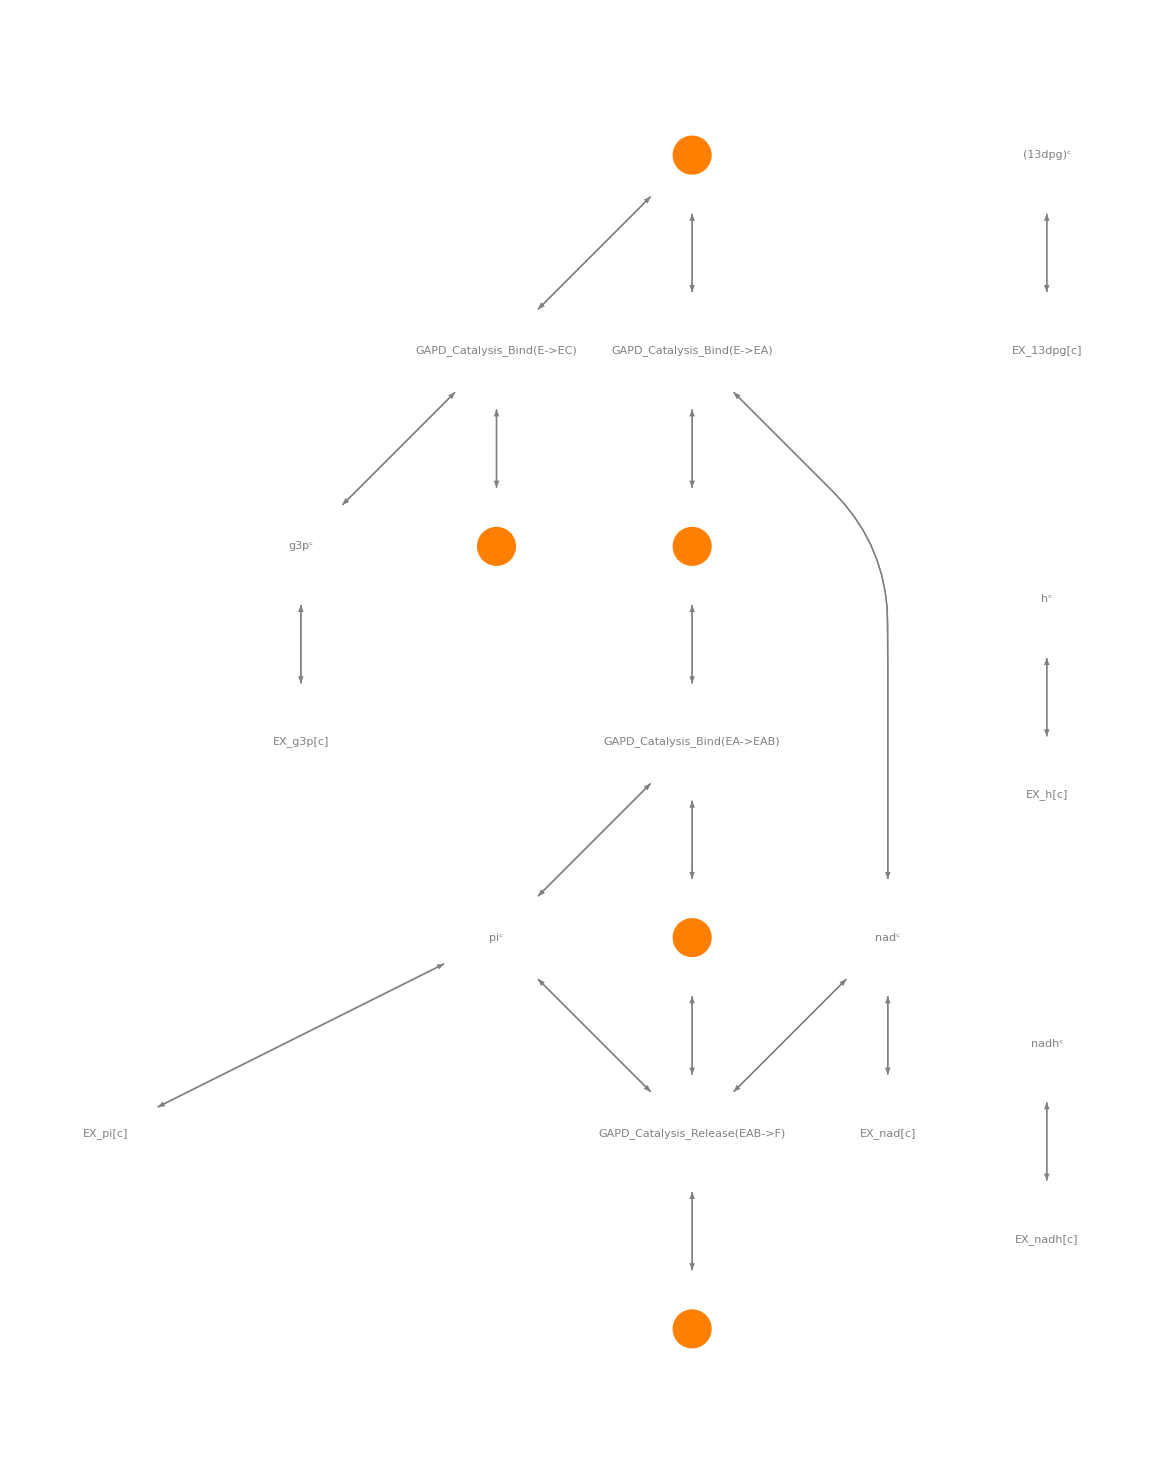

```mathematica
visualizePathways@gapdEnzyme
```